## Basics

```mathematica
dim=3;
d=2;
variables=Table[Subscript[ξ, j],{j,1,dim}];
```

### Noncommutative multiply changes

```mathematica
Unprotect[NonCommutativeMultiply];
NonCommutativeMultiply[m1__List,m2__List]:=Inner[NonCommutativeMultiply,m1,m2,Plus];
NonCommutativeMultiply[m1__List,m2_]:= Map[NonCommutativeMultiply[#1,m2]&,m1];
NonCommutativeMultiply[m1_,m2__List]:= Map[NonCommutativeMultiply[m1,#1]&,m2];
Protect[NonCommutativeMultiply];
```

### Derivations on T_θ

```mathematica
Element[Subscript[ξ, 1],Reals];
Element[Subscript[ξ, 2],Reals];
Element[Subscript[ξ, 3],Reals];
Others={ξ,1/(1+ξ^2)};
δ[a_,list_]:=If[list[[1]]≠ 0,δ[Subscript[δ, 1][a],list-{1,0,0}],If[list[[2]]≠0,δ[Subscript[δ, 2][a],list-{0,1,0}],If[list[[3]]≠0,δ[Subscript[δ, 3][a],list-{0,0,1}],a]]];
Subscript[δ, j_][x__+y_]:= Subscript[δ, j][x]+Subscript[δ, j][y];
Subscript[δ, j_][x_^n_. *k_]/;Or[MemberQ[variables,x],Element[x,Integers],Element[x,Complexes],Element[x,Reals]]:=x^n*Subscript[δ, j][k];
(*Subscript[δ, j_][x_^n_. *kk_]:=x^n*Subscript[δ, j][kk]*)
(*Subscript[δ, j_][a_^*]:=-(Subscript[δ, j][a])^*;*)
SuperStar[Subscript[δ, j_][a_]]:=-Subscript[δ, j][SuperStar[a]];
Subscript[δ, j_][I]:=0;
Subscript[δ, j_][0]:=0;
Subscript[δ, j_][x__**y_]:= Subscript[δ, j][x]**y+x**Subscript[δ, j][y];
Subscript[δ, j_][list__List]:=Map[Subscript[δ, j],list];
Subscript[δ, j_][Subscript[ξ, i_]^n_]:=0;
```

### Noncommutative Multiply

```mathematica
NCM={(x_+y_)**z_->(x**z)+(y**z),
x_**(y_+z_)->( x**y)+(x**z),
x_**(y_^n_.*z_)/;Or[MemberQ[variables,y],MemberQ[Others,y],Element[y,Integers],Element[y,Complexes],Element[x,Reals]]->y^n* (x**z),(y_^n_.*z_)**x_/;Or[MemberQ[variables,y],MemberQ[Others,y],Element[y,Integers],Element[y,Complexes],Element[x,Reals]]->y^n* (z**x),
x_**0-> 0,
0**x_-> 0};
```

### Derivatives of b_0

```mathematica
Der:={
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 1]]-> - 2 Subscript[ξ, 1] k^2**Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 2]]-> - 2 Subscript[ξ, 2] k^2**Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],Subscript[ξ, 3]]->  -2 Subscript[ξ, 3] Subscript[b, 0]^2,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],2}]->  -2 k^2**Subscript[b, 0]^2+8 Subscript[ξ, 1]^2 k^4**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 2],2}]->  -2 k^2**Subscript[b, 0]^2+8 Subscript[ξ, 2]^2 k^4**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 3],2}]-> - 2 Subscript[b, 0]^2+8 Subscript[ξ, 3]^2 Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],1},{Subscript[ξ, 2],1}]->  8 Subscript[ξ, 1] Subscript[ξ, 2] k^4**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 1],1},{Subscript[ξ, 3],1}]->  8 Subscript[ξ, 1] Subscript[ξ, 3] k^2**Subscript[b, 0]^3,
D[Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]],{Subscript[ξ, 2],1},{Subscript[ξ, 3],1}]->  8 Subscript[ξ, 2] Subscript[ξ, 3] k^2**Subscript[b, 0]^3
(*,δ1[k^2 (τ1^2+τ2^2)]-> τ1^2 δ1[k^2 ]+τ2^2 δ1[k^2 ],δ2[k^2 (τ1^2+τ2^2)]-> τ1^2 δ2[k^2 ]+τ2^2 δ2[k^2 ]*)};
```

## Symbol of the Laplacian and b_2

### Symbol of the Laplacian on Functions

```mathematica
Subscript[a, 2]={{k^2 Subscript[ξ, 1]^2+k^2 Subscript[ξ, 2]^2+Subscript[ξ, 3]^2,0,0},{0,k^2 Subscript[ξ, 1]^2+k^2 Subscript[ξ, 2]^2+Subscript[ξ, 3]^2,0},{0,0,k^2 Subscript[ξ, 1]^2+k^2 Subscript[ξ, 2]^2+Subscript[ξ, 3]^2}};
Subscript[a, 1]={{Subscript[ξ, 1] Subscript[δ, 1][k^2]+Subscript[ξ, 2] Subscript[δ, 2][k^2],Subscript[ξ, 2] Subscript[δ, 1][k^2]-Subscript[ξ, 1] Subscript[δ, 2][k^2],-Subscript[δ, 3][k^2]**(1/k) Subscript[ξ, 1]},{-Subscript[ξ, 2] Subscript[δ, 1][k^2]+Subscript[ξ, 1] Subscript[δ, 2][k^2],Subscript[ξ, 1] Subscript[δ, 1][k^2]+Subscript[ξ, 2] Subscript[δ, 2][k^2],-Subscript[δ, 3][k^2]**(1/k) Subscript[ξ, 2]},{(1/k)**Subscript[δ, 3][k^2] Subscript[ξ, 1],(1/k)**Subscript[δ, 3][k^2] Subscript[ξ, 2],2 k**Subscript[δ, 1][k] Subscript[ξ, 1]+2 k**Subscript[δ, 2][k] Subscript[ξ, 2]+2 (1/k)**Subscript[δ, 3][k] Subscript[ξ, 3]-(1/k)**Subscript[δ, 3][k^2]**(1/k) Subscript[ξ, 3]}};
Subscript[a, 0]={{0,0,-Subscript[δ, 1][Subscript[δ, 3][k^2]]**(1/k)-Subscript[δ, 3][k^2]**(1/k^2)**Subscript[δ, 1][k]-Subscript[δ, 3][k^2]**Subscript[δ, 1][1/k^2]**k+Subscript[δ, 1][Subscript[δ, 3][k]]-Subscript[δ, 3][Subscript[δ, 1][k]]},{0,0,-Subscript[δ, 2][Subscript[δ, 3][k^2]]**(1/k)-Subscript[δ, 3][k^2]**(1/k^2)**Subscript[δ, 2][k]-Subscript[δ, 3][k^2]**Subscript[δ, 2][1/k^2]**k+Subscript[δ, 2][Subscript[δ, 3][k]]-Subscript[δ, 3][Subscript[δ, 2][k]]},{0,0,(1/k)**Subscript[δ, 3][Subscript[δ, 3][k]]+k**Subscript[δ, 1][Subscript[δ, 1][k]]+k**Subscript[δ, 2][Subscript[δ, 2][k]]-(1/k)**Subscript[δ, 3][Subscript[δ, 3][k^2]]**(1/k)-(1/k)**Subscript[δ, 3][k^2]**(1/k^2)**Subscript[δ, 3][k]-(1/k)**Subscript[δ, 3][k^2]**Subscript[δ, 3][1/k^2]**k}};
```

### Recursive Formula for the expansion of the symbol of the Parametrix

```mathematica
dD[r_,p_,α_]:=Sum[1/((Subscript[i, 1])!*(Subscript[i, 2])!*(α-Subscript[i, 1]-Subscript[i, 2])!)D[r,{Subscript[ξ, 1],Subscript[i, 1]},{Subscript[ξ, 2],Subscript[i, 2]},{Subscript[ξ, 3],α-Subscript[i, 1]-Subscript[i, 2]}]**δ[p,{Subscript[i, 1],Subscript[i, 2],α-Subscript[i, 1]-Subscript[i, 2]}],{Subscript[i, 2],0,α},{Subscript[i, 1],0,α-Subscript[i, 2]}];
b[0]:=Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]]IdentityMatrix[dim];
b[n_]:=-Sum[(dD[b[j],Subscript[a, kk],n-j-d+kk]),{kk,0,d},{j,0,n-1}]**b[0];
```

```mathematica
Expand[b[2]//.NCM//.Der//.NCM]//.{Subscript[δ, j_][1]->0}//.Subscript[b, 0][Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3]]->Subscript[b, 0]
```

{{b_0^2**δ_3[δ_3[k^2]]**b_0 ξ_1^2+3 k^2**b_0^2**δ_1[δ_1[k^2]]**b_0 ξ_1^2+k^2**b_0^2**δ_2[δ_2[k^2]]**b_0 ξ_1^2+155+4 b_0^2**δ_3[k^2]**b_0^2**δ_3[k^2]**b_0 ξ_2^4 ξ_3^2+8 b_0^3**δ_3[k^2]**b_0**δ_3[k^2]**b_0 ξ_2^4 ξ_3^2,1,1},{1},{1}}
 |  |  |  |

```mathematica
Expand[Expand[%//.NCM//.{x_**1->x,0**x_-> 0,x_**0->0,1**x_->x, k^(n_.)**k^(m_.)-> k^(n+m)}]//.NCM//.Subscript[δ, j_][k^n_]/;n≤-1->-k^n **Subscript[δ, j][k^-n]**k^n//.Subscript[δ, j_][k^n_]/;n>1-> Subscript[δ, j][k]**k^(n-1)+k**Subscript[δ, j][k^(n-1)]//.NCM//.{x_**1->x,0**x_-> 0,x_**0->0,1**x_->x, k^(n_.)**k^(m_.)-> k^(n+m)}]
```

{{b_0^2**k**δ_3[δ_3[k]]**b_0 ξ_1^2+2 b_0^2**δ_3[k]**δ_3[k]**b_0 ξ_1^2+b_0^2**δ_3[δ_3[k]]**k**b_0 ξ_1^2+615+8 b_0^3**δ_3[k]**k**b_0**k**δ_3[k]**b_0 ξ_2^4 ξ_3^2+8 b_0^3**δ_3[k]**k**b_0**δ_3[k]**k**b_0 ξ_2^4 ξ_3^2,1,1},{1},{1}}
 |  |  |  |

## Integration and Rearrangement Lemma

### Angle Integration

```mathematica
polar={Subscript[ξ, 1]->√(u*(1+η^2))*Cos[θ],Subscript[ξ, 2]->√(u*(1+η^2))*Sin[θ],Subscript[ξ, 3]->η};
Intheta[a_]:=Integrate[(a/.x_NonCommutativeMultiply->1/.polar)*(1+η^2)/2,{θ,0,2π}] a/(a/.x_NonCommutativeMultiply->1);
Intheta[a_+b_]:=Intheta[a]+Intheta[b];
Attributes[Intheta]={Listable};
```

```mathematica
Intxi[temp_]:=Integrate[(temp/.NonCommutativeMultiply->Times/.c_*Subscript[b, 0]^(power_.)->(1+η^2)^-power)temp,{η,-Infinity,Infinity}];
Intxi[a_+b_]:=Intxi[a]+Intxi[b];
Attributes[Intxi]={Listable};
```

```mathematica
Intxi[Intheta[Out[31]]]
```

{{π^2 u b_0^2**k**δ_3[δ_3[k]]**b_0+2 π^2 u b_0^2**δ_3[k]**δ_3[k]**b_0+π^2 u b_0^2**δ_3[δ_3[k]]**k**b_0-2 π^2 u b_0^3**k**δ_3[δ_3[k]]**b_0-4 π^2 u b_0^3**δ_3[k]**δ_3[k]**b_0-2 π^2 u b_0^3**δ_3[δ_3[k]]**k**b_0+2 π^2 u k^2**b_0^2**k**δ_1[δ_1[k]]**b_0+2 π^2 u k^2**b_0^2**k**δ_2[δ_2[k]]**b_0+4 π^2 u k^2**b_0^2**δ_1[k]**δ_1[k]**b_0+2 π^2 u k^2**b_0^2**δ_1[δ_1[k]]**k**b_0+4 π^2 u k^2**b_0^2**δ_2[k]**δ_2[k]**b_0+2 π^2 u k^2**b_0^2**δ_2[δ_2[k]]**k**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_1[δ_1[k]]**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_2[δ_2[k]]**b_0-4 π^2 u^2 k^4**b_0^3**δ_1[k]**δ_1[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_1[δ_1[k]]**k**b_0-4 π^2 u^2 k^4**b_0^3**δ_2[k]**δ_2[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_2[δ_2[k]]**k**b_0-1/2 π^2 u b_0**δ_3[k]**b_0**δ_3[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**k**δ_1[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**δ_1[k]**k**b_0+π^2 u b_0**k**δ_2[k]**b_0**k**δ_2[k]**b_0+π^2 u b_0**k**δ_2[k]**b_0**δ_2[k]**k**b_0-1/2 π^2 u b_0**k**δ_3[k]**1/k**b_0**δ_3[k]**b_0+π^2 u b_0**δ_1[k]**k**b_0**k**δ_1[k]**b_0+π^2 u b_0**δ_1[k]**k**b_0**δ_1[k]**k**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**δ_1[k]**k**b_0+π^2 u b_0**δ_2[k]**k**b_0**k**δ_2[k]**b_0+π^2 u b_0**δ_2[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**δ_2[k]**k**b_0-1/2 π^2 u b_0**δ_3[k]**b_0**1/k**δ_3[k]**k**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**δ_3[k]**k**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**δ_3[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**k**δ_1[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**δ_1[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**k**δ_2[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**δ_2[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**k**δ_1[k]**b_0-6 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**δ_1[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**k**δ_2[k]**b_0-6 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0-1/2 π^2 u b_0**k**δ_3[k]**1/k**b_0**1/k**δ_3[k]**k**b_0,-π^2 u k^2**b_0^2**k**δ_1[δ_2[k]]**b_0+π^2 u k^2**b_0^2**k**δ_2[δ_1[k]]**b_0-π^2 u k^2**b_0^2**δ_1[δ_2[k]]**k**b_0+π^2 u k^2**b_0^2**δ_2[δ_1[k]]**k**b_0+π^2 u b_0**k**δ_1[k]**b_0**k**δ_2[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**δ_2[k]**k**b_0-π^2 u b_0**k**δ_2[k]**b_0**k**δ_1[k]**b_0-π^2 u b_0**k**δ_2[k]**b_0**δ_1[k]**k**b_0+π^2 u b_0**δ_1[k]**k**b_0**k**δ_2[k]**b_0+π^2 u b_0**δ_1[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**δ_2[k]**k**b_0-π^2 u b_0**δ_2[k]**k**b_0**k**δ_1[k]**b_0-π^2 u b_0**δ_2[k]**k**b_0**δ_1[k]**k**b_0+π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**k**δ_1[k]**b_0+π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**δ_1[k]**k**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**δ_2[k]**k**b_0+π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**k**δ_1[k]**b_0+π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**δ_1[k]**k**b_0,π^2 b_0**δ_3[δ_1[k]]**b_0-π^2 u k^2**b_0^2**δ_1[δ_3[k]]**b_0+π^2 b_0**k**δ_1[δ_3[k]]**1/k**b_0+π^2 b_0**δ_1[k]**δ_3[k]**1/k**b_0-π^2 u k^2**b_0^2**k**δ_1[δ_3[k]]**1/k**b_0-π^2 u k^2**b_0^2**δ_1[k]**δ_3[k]**1/k**b_0-π^2 u b_0**k**δ_1[k]**b_0**δ_3[k]**b_0-π^2 u b_0**δ_1[k]**k**b_0**δ_3[k]**b_0-2 π^2 u b_0**δ_3[k]**b_0**k**δ_1[k]**b_0-π^2 u b_0**δ_3[k]**b_0**δ_1[k]**k**b_0+π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**δ_3[k]**b_0+π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**δ_3[k]**b_0+π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**k**δ_1[k]**b_0+π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**δ_1[k]**k**b_0-π^2 b_0**k**δ_3[k]**1/k**δ_1[k]**1/k**b_0+π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**k**δ_1[k]**b_0+π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**δ_1[k]**k**b_0+π^2 u k^2**b_0^2**k**δ_3[k]**1/k**δ_1[k]**1/k**b_0-π^2 u b_0**k**δ_1[k]**b_0**k**δ_3[k]**1/k**b_0-2 π^2 u b_0**k**δ_3[k]**1/k**b_0**k**δ_1[k]**b_0-π^2 u b_0**k**δ_3[k]**1/k**b_0**δ_1[k]**k**b_0+π^2 u^2 b_0**k**δ_3[k]**k**b_0^2**k**δ_1[k]**b_0+π^2 u^2 b_0**k**δ_3[k]**k**b_0^2**δ_1[k]**k**b_0-π^2 u b_0**δ_1[k]**k**b_0**k**δ_3[k]**1/k**b_0+π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**k**δ_3[k]**1/k**b_0+π^2 u^2 k^2**b_0^2**k**δ_3[k]**1/k**b_0**k**δ_1[k]**b_0+π^2 u^2 k^2**b_0^2**k**δ_3[k]**1/k**b_0**δ_1[k]**k**b_0+π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**k**δ_3[k]**1/k**b_0},{π^2 u k^2**b_0^2**k**δ_1[δ_2[k]]**b_0-π^2 u k^2**b_0^2**k**δ_2[δ_1[k]]**b_0+π^2 u k^2**b_0^2**δ_1[δ_2[k]]**k**b_0-π^2 u k^2**b_0^2**δ_2[δ_1[k]]**k**b_0-π^2 u b_0**k**δ_1[k]**b_0**k**δ_2[k]**b_0-π^2 u b_0**k**δ_1[k]**b_0**δ_2[k]**k**b_0+π^2 u b_0**k**δ_2[k]**b_0**k**δ_1[k]**b_0+π^2 u b_0**k**δ_2[k]**b_0**δ_1[k]**k**b_0-π^2 u b_0**δ_1[k]**k**b_0**k**δ_2[k]**b_0-π^2 u b_0**δ_1[k]**k**b_0**δ_2[k]**k**b_0+π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**k**δ_2[k]**b_0+π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**δ_2[k]**k**b_0+π^2 u b_0**δ_2[k]**k**b_0**k**δ_1[k]**b_0+π^2 u b_0**δ_2[k]**k**b_0**δ_1[k]**k**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**δ_1[k]**k**b_0+π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**k**δ_2[k]**b_0+π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**δ_2[k]**k**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**δ_1[k]**k**b_0,π^2 u b_0^2**k**δ_3[δ_3[k]]**b_0+2 π^2 u b_0^2**δ_3[k]**δ_3[k]**b_0+π^2 u b_0^2**δ_3[δ_3[k]]**k**b_0-2 π^2 u b_0^3**k**δ_3[δ_3[k]]**b_0-4 π^2 u b_0^3**δ_3[k]**δ_3[k]**b_0-2 π^2 u b_0^3**δ_3[δ_3[k]]**k**b_0+2 π^2 u k^2**b_0^2**k**δ_1[δ_1[k]]**b_0+2 π^2 u k^2**b_0^2**k**δ_2[δ_2[k]]**b_0+4 π^2 u k^2**b_0^2**δ_1[k]**δ_1[k]**b_0+2 π^2 u k^2**b_0^2**δ_1[δ_1[k]]**k**b_0+4 π^2 u k^2**b_0^2**δ_2[k]**δ_2[k]**b_0+2 π^2 u k^2**b_0^2**δ_2[δ_2[k]]**k**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_1[δ_1[k]]**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_2[δ_2[k]]**b_0-4 π^2 u^2 k^4**b_0^3**δ_1[k]**δ_1[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_1[δ_1[k]]**k**b_0-4 π^2 u^2 k^4**b_0^3**δ_2[k]**δ_2[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_2[δ_2[k]]**k**b_0-1/2 π^2 u b_0**δ_3[k]**b_0**δ_3[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**k**δ_1[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**δ_1[k]**k**b_0+π^2 u b_0**k**δ_2[k]**b_0**k**δ_2[k]**b_0+π^2 u b_0**k**δ_2[k]**b_0**δ_2[k]**k**b_0-1/2 π^2 u b_0**k**δ_3[k]**1/k**b_0**δ_3[k]**b_0+π^2 u b_0**δ_1[k]**k**b_0**k**δ_1[k]**b_0+π^2 u b_0**δ_1[k]**k**b_0**δ_1[k]**k**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**δ_1[k]**k^3**b_0^2**δ_1[k]**k**b_0+π^2 u b_0**δ_2[k]**k**b_0**k**δ_2[k]**b_0+π^2 u b_0**δ_2[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**δ_2[k]**k^3**b_0^2**δ_2[k]**k**b_0-1/2 π^2 u b_0**δ_3[k]**b_0**1/k**δ_3[k]**k**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**δ_3[k]**k**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**δ_3[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**k**δ_1[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**δ_1[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**k**δ_2[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**δ_2[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**k**δ_1[k]**b_0-6 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**δ_1[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**k**δ_2[k]**b_0-6 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0-1/2 π^2 u b_0**k**δ_3[k]**1/k**b_0**1/k**δ_3[k]**k**b_0,π^2 b_0**δ_3[δ_2[k]]**b_0-π^2 u k^2**b_0^2**δ_2[δ_3[k]]**b_0+π^2 b_0**k**δ_2[δ_3[k]]**1/k**b_0+π^2 b_0**δ_2[k]**δ_3[k]**1/k**b_0-π^2 u k^2**b_0^2**k**δ_2[δ_3[k]]**1/k**b_0-π^2 u k^2**b_0^2**δ_2[k]**δ_3[k]**1/k**b_0-π^2 u b_0**k**δ_2[k]**b_0**δ_3[k]**b_0-π^2 u b_0**δ_2[k]**k**b_0**δ_3[k]**b_0-2 π^2 u b_0**δ_3[k]**b_0**k**δ_2[k]**b_0-π^2 u b_0**δ_3[k]**b_0**δ_2[k]**k**b_0+π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**δ_3[k]**b_0+π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**δ_3[k]**b_0+π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**k**δ_2[k]**b_0+π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**δ_2[k]**k**b_0-π^2 b_0**k**δ_3[k]**1/k**δ_2[k]**1/k**b_0+π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**k**δ_2[k]**b_0+π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**δ_2[k]**k**b_0+π^2 u k^2**b_0^2**k**δ_3[k]**1/k**δ_2[k]**1/k**b_0-π^2 u b_0**k**δ_2[k]**b_0**k**δ_3[k]**1/k**b_0-2 π^2 u b_0**k**δ_3[k]**1/k**b_0**k**δ_2[k]**b_0-π^2 u b_0**k**δ_3[k]**1/k**b_0**δ_2[k]**k**b_0+π^2 u^2 b_0**k**δ_3[k]**k**b_0^2**k**δ_2[k]**b_0+π^2 u^2 b_0**k**δ_3[k]**k**b_0^2**δ_2[k]**k**b_0-π^2 u b_0**δ_2[k]**k**b_0**k**δ_3[k]**1/k**b_0+π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**k**δ_3[k]**1/k**b_0+π^2 u^2 k^2**b_0^2**k**δ_3[k]**1/k**b_0**k**δ_2[k]**b_0+π^2 u^2 k^2**b_0^2**k**δ_3[k]**1/k**b_0**δ_2[k]**k**b_0+π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**k**δ_3[k]**1/k**b_0},{π^2 u k^2**b_0^2**δ_1[δ_3[k]]**b_0+π^2 u k^2**b_0^2**1/k**δ_1[δ_3[k]]**k**b_0+π^2 u k^2**b_0^2**1/k**δ_3[k]**δ_1[k]**b_0+π^2 u b_0**k**δ_1[k]**b_0**δ_3[k]**b_0+π^2 u b_0**δ_3[k]**b_0**k**δ_1[k]**b_0+π^2 u b_0**δ_3[k]**b_0**δ_1[k]**k**b_0-π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**δ_3[k]**b_0-π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**δ_3[k]**b_0-π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**k**δ_1[k]**b_0-π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**δ_1[k]**k**b_0-π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**δ_1[k]**k**b_0-π^2 u k^2**b_0^2**1/k**δ_1[k]**1/k**δ_3[k]**k**b_0+π^2 u b_0**1/k**δ_3[k]**k**b_0**k**δ_1[k]**b_0+π^2 u b_0**1/k**δ_3[k]**k**b_0**δ_1[k]**k**b_0-π^2 u^2 b_0**1/k**δ_3[k]**k^3**b_0^2**k**δ_1[k]**b_0-π^2 u^2 b_0**1/k**δ_3[k]**k^3**b_0^2**δ_1[k]**k**b_0+π^2 u b_0**k**δ_1[k]**b_0**1/k**δ_3[k]**k**b_0-π^2 u^2 k^2**b_0^2**1/k**δ_3[k]**k**b_0**k**δ_1[k]**b_0-π^2 u^2 k^2**b_0^2**1/k**δ_3[k]**k**b_0**δ_1[k]**k**b_0-π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**1/k**δ_3[k]**k**b_0-π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**1/k**δ_3[k]**k**b_0,π^2 u k^2**b_0^2**δ_2[δ_3[k]]**b_0+π^2 u k^2**b_0^2**1/k**δ_2[δ_3[k]]**k**b_0+π^2 u k^2**b_0^2**1/k**δ_3[k]**δ_2[k]**b_0+π^2 u b_0**k**δ_2[k]**b_0**δ_3[k]**b_0+π^2 u b_0**δ_3[k]**b_0**k**δ_2[k]**b_0+π^2 u b_0**δ_3[k]**b_0**δ_2[k]**k**b_0-π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**δ_3[k]**b_0-π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**δ_3[k]**b_0-π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**k**δ_2[k]**b_0-π^2 u^2 k^2**b_0^2**δ_3[k]**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**δ_3[k]**k^2**b_0^2**δ_2[k]**k**b_0-π^2 u k^2**b_0^2**1/k**δ_2[k]**1/k**δ_3[k]**k**b_0+π^2 u b_0**1/k**δ_3[k]**k**b_0**k**δ_2[k]**b_0+π^2 u b_0**1/k**δ_3[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 b_0**1/k**δ_3[k]**k^3**b_0^2**k**δ_2[k]**b_0-π^2 u^2 b_0**1/k**δ_3[k]**k^3**b_0^2**δ_2[k]**k**b_0+π^2 u b_0**k**δ_2[k]**b_0**1/k**δ_3[k]**k**b_0-π^2 u^2 k^2**b_0^2**1/k**δ_3[k]**k**b_0**k**δ_2[k]**b_0-π^2 u^2 k^2**b_0^2**1/k**δ_3[k]**k**b_0**δ_2[k]**k**b_0-π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**1/k**δ_3[k]**k**b_0-π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**1/k**δ_3[k]**k**b_0,-π^2 b_0**k**δ_1[δ_1[k]]**b_0-π^2 b_0**k**δ_2[δ_2[k]]**b_0+π^2 b_0**δ_3[δ_3[k]]**1/k**b_0+π^2 b_0^2**1/k**δ_3[δ_3[k]]**b_0+π^2 u b_0^2**k**δ_3[δ_3[k]]**b_0+2 π^2 u b_0^2**δ_3[k]**δ_3[k]**b_0-π^2 b_0^2**δ_3[δ_3[k]]**1/k**b_0+π^2 u b_0^2**δ_3[δ_3[k]]**k**b_0-2 π^2 u b_0^3**k**δ_3[δ_3[k]]**b_0-4 π^2 u b_0^3**δ_3[k]**δ_3[k]**b_0-2 π^2 u b_0^3**δ_3[δ_3[k]]**k**b_0+3 π^2 u k^2**b_0^2**k**δ_1[δ_1[k]]**b_0+3 π^2 u k^2**b_0^2**k**δ_2[δ_2[k]]**b_0+4 π^2 u k^2**b_0^2**δ_1[k]**δ_1[k]**b_0+π^2 u k^2**b_0^2**δ_1[δ_1[k]]**k**b_0+4 π^2 u k^2**b_0^2**δ_2[k]**δ_2[k]**b_0+π^2 u k^2**b_0^2**δ_2[δ_2[k]]**k**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_1[δ_1[k]]**b_0-2 π^2 u^2 k^4**b_0^3**k**δ_2[δ_2[k]]**b_0-4 π^2 u^2 k^4**b_0^3**δ_1[k]**δ_1[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_1[δ_1[k]]**k**b_0-4 π^2 u^2 k^4**b_0^3**δ_2[k]**δ_2[k]**b_0-2 π^2 u^2 k^4**b_0^3**δ_2[δ_2[k]]**k**b_0-π^2 u b_0**δ_3[k]**b_0**δ_3[k]**b_0+π^2 b_0**1/k**δ_3[k]**δ_3[k]**1/k**b_0-π^2 b_0**δ_3[k]**1/k**δ_3[k]**1/k**b_0-π^2 b_0^2**1/k**δ_3[k]**1/k**δ_3[k]**b_0+π^2 b_0^2**δ_3[k]**1/k**δ_3[k]**1/k**b_0-π^2 u b_0**1/k**δ_3[k]**k**b_0**δ_3[k]**b_0+1/2 π^2 b_0**1/k**δ_3[k]**b_0**1/k**δ_3[k]**b_0+π^2 u b_0**1/k**δ_3[k]**b_0**k**δ_3[k]**b_0-1/2 π^2 b_0**1/k**δ_3[k]**b_0**δ_3[k]**1/k**b_0+π^2 u b_0**1/k**δ_3[k]**b_0**δ_3[k]**k**b_0-π^2 u b_0**1/k**δ_3[k]**b_0^2**k**δ_3[k]**b_0-π^2 u b_0**1/k**δ_3[k]**b_0^2**δ_3[k]**k**b_0+4 π^2 u b_0**k**δ_1[k]**b_0**k**δ_1[k]**b_0+2 π^2 u b_0**k**δ_1[k]**b_0**δ_1[k]**k**b_0+4 π^2 u b_0**k**δ_2[k]**b_0**k**δ_2[k]**b_0+2 π^2 u b_0**k**δ_2[k]**b_0**δ_2[k]**k**b_0-1/2 π^2 b_0**δ_3[k]**1/k**b_0**1/k**δ_3[k]**b_0-π^2 u b_0**δ_3[k]**1/k**b_0**k**δ_3[k]**b_0+1/2 π^2 b_0**δ_3[k]**1/k**b_0**δ_3[k]**1/k**b_0-π^2 u b_0**δ_3[k]**1/k**b_0**δ_3[k]**k**b_0+π^2 u b_0**δ_3[k]**1/k**b_0^2**k**δ_3[k]**b_0+π^2 u b_0**δ_3[k]**1/k**b_0^2**δ_3[k]**k**b_0-π^2 u b_0**δ_3[k]**b_0**k**δ_3[k]**1/k**b_0-π^2 u b_0^2**1/k**δ_3[k]**b_0**k**δ_3[k]**b_0-π^2 u b_0^2**1/k**δ_3[k]**b_0**δ_3[k]**k**b_0-π^2 u b_0^2**k**δ_3[k]**b_0**1/k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**k**δ_3[k]**b_0+π^2 u b_0^2**k**δ_3[k]**b_0**δ_3[k]**1/k**b_0-2 π^2 u^2 b_0^2**k**δ_3[k]**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**k**δ_3[k]**b_0^2**δ_3[k]**k**b_0+π^2 u b_0^2**δ_3[k]**1/k**b_0**k**δ_3[k]**b_0+π^2 u b_0^2**δ_3[k]**1/k**b_0**δ_3[k]**k**b_0-π^2 u b_0^2**δ_3[k]**k**b_0**1/k**δ_3[k]**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**k**δ_3[k]**b_0+π^2 u b_0^2**δ_3[k]**k**b_0**δ_3[k]**1/k**b_0-2 π^2 u^2 b_0^2**δ_3[k]**k**b_0**δ_3[k]**k**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**k**δ_3[k]**b_0+2 π^2 u^2 b_0^2**δ_3[k]**k**b_0^2**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**k**δ_3[k]**b_0**δ_3[k]**k**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**k**δ_3[k]**b_0+4 π^2 u^2 b_0^3**δ_3[k]**k**b_0**δ_3[k]**k**b_0-8 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**k**δ_1[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_1[k]**b_0**δ_1[k]**k**b_0-8 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**k**δ_2[k]**b_0-6 π^2 u^2 k^2**b_0^2**k**δ_2[k]**b_0**δ_2[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**k**δ_1[k]**b_0-4 π^2 u^2 k^2**b_0^2**δ_1[k]**k**b_0**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_1[k]**k^3**b_0^2**δ_1[k]**k**b_0-6 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**k**δ_2[k]**b_0-4 π^2 u^2 k^2**b_0^2**δ_2[k]**k**b_0**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**δ_2[k]**k^3**b_0^2**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_1[k]**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**k**δ_2[k]**b_0**δ_2[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**k**δ_1[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_1[k]**k**b_0**δ_1[k]**k**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**k**δ_2[k]**b_0+4 π^2 u^3 k^4**b_0^3**δ_2[k]**k**b_0**δ_2[k]**k**b_0-2 π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0-2 π^2 u^2 b_0**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0-2 π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0-2 π^2 u^2 b_0**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**k**δ_1[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_1[k]**k^2**b_0^2**δ_1[k]**k**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**k**δ_2[k]**b_0+2 π^2 u^3 k^2**b_0^2**k**δ_2[k]**k^2**b_0^2**δ_2[k]**k**b_0-π^2 u b_0**1/k**δ_3[k]**k**b_0**k**δ_3[k]**1/k**b_0}}

## Rearrangement Lemma

```mathematica
powkinmod=2;(*Δ[a]=k^-powkinmod ak^powkinmod*)
powkinb=2;(*Subscript[b, 0](u)=(1+uk^powkinb0)^-1*)
RearrangeLemma[input_,pkm_:powkinmod,pkb_:powkinb]:=Module[{term,coef,Cpart,NCpart,NCelements,withoutkNCpart,kpowinright,listofpowofb,changes},
term=input/.Subscript[δ, j_][a_]->k**Subscript[invkδ, j][a];(*Subscript[invkδ, j][a] represents k^-1 Subscript[δ, j][a] and it is the form of the elements we want to have in the final result so that we can change Subscript[δ, j][log[k]]*)
listofpowofb=DeleteCases[Exponent[term/.NonCommutativeMultiply->List,Subscript[b, 0]],0];
Cpart=term/.NonCommutativeMultiply[L_]->1;(*Cpart is the commutative part of the term*)
coef=Cpart/.u->1;(*coef is the constant part of the term*)
NCpart=term/Cpart;(*NCpart is the noncommutative part of the term*)
withoutkNCpart=DeleteCases[Table[If[(kpowinright=Exponent[NCpart[[j;;]]/.NonCommutativeMultiply->Times,k])==0||Or[MemberQ[{#}, Subscript[b, 0]^(n_.)],MemberQ[{#}, k^(n_.)]]&[NCpart[[j]]],NCpart[[j]],Δ^(kpowinright/pkm)NCpart[[j]]],{j,1,Length[NCpart]}],k^(n_.)]/.List->NonCommutativeMultiply;(*in withoutkNCpart we have gotten rid out of k in the middles othe terms. ks are brought to the left and we have used the identity kΔ^(kpowinright/powkinmod)[a]=ak^kpowinright where kpowinright is the number of k after the element in term*)
NCelements=DeleteCases[DeleteCases[Split[withoutkNCpart/.NonCommutativeMultiply->List,Not[MemberQ[{#}, Subscript[b, 0]^(n_.)]]&],Subscript[b, 0]^(somepow_.),2],{}];
(*Done by Rui Beginning*)
(*In this situation the problem probably happens only when Length[listofpowofb]=2, thus only need to insert a 0 when Length[listofpowofb]=2, and everything is fine when Length[listofpowofb]=3. In general case maybe this does not work.*)
(*If[Length[Flatten[NCelements]]≠Length[NCelements],{NCelements=Transpose[NCelements],listofpowofb=Insert[listofpowofb,0,2]}];*)(*How do you know that the zero shouldd be added in the second place?*)
(*Done by Rui End*)changes=1;
For[counter=1,counter≤Length[NCelements],counter++,If[Length[NCelements[[counter]]]≠ 1,listofpowofb=Insert[listofpowofb,0,counter+changes];changes++];];
Return[coef *k^(-(Exponent[term,u]+1)*pkb+Exponent[term/.NonCommutativeMultiply->Times,k])*Subscript[F, Exponent[term,u],listofpowofb][Delete[Table[Subscript[t, j],{j,1,Length[listofpowofb]-1}],0]]ReplacePart[Table[Subscript[t, j],{j,1,Length[listofpowofb]-1}]^Exponent[Flatten[NCelements],Δ],0-> Times]NCPart[Delete[Flatten[(NCelements/.Subscript[invkδ, j_][a_]->k^-1**Subscript[δ, j][a])]/.Δ->1,0]]]
]
RearrangeLemma[x_+y_]:=RearrangeLemma[x]+RearrangeLemma[y];
Attributes[RearrangeLemma]=Listable;
```

```mathematica
RearrangeLemma[Out[39]]
```

{{2 π^2 NCPart[1/k**δ_1[δ_1[k]]] F_(1,{2,1})[t_1]+2 π^2 NCPart[1/k**δ_2[δ_2[k]]] F_(1,{2,1})[t_1]+104+4 π^2 NCPart[1/k**δ_2[k],1/k**δ_2[k]] t_1^(3/2) √t_2 F_(3,{3,1,1})[t_1,t_2],1,1/k+38+1/k},{1},{1}}
 |  |  |  |

## Put the outcome of the Rearrangement Lemma in good form

```mathematica
functiontwokδ1δ1[t1_,t2_]:=Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][k],(1/k)**Subscript[δ, 1][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2};
functiontwokδ2δ2[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][k],(1/k)**Subscript[δ, 2][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ3δ3[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][k],(1/k)**Subscript[δ, 3][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ1δ3[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][k],(1/k)**Subscript[δ, 3][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ3δ1[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][k],(1/k)**Subscript[δ, 1][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ1δ2[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][k],(1/k)**Subscript[δ, 2][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ2δ1[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][k],(1/k)**Subscript[δ, 1][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ2δ3[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][k],(1/k)**Subscript[δ, 3][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiontwokδ3δ2[t1_,t2_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][k],(1/k)**Subscript[δ, 2][k]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})

functiononekδ1δ1[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][Subscript[δ, 1][k]]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiononekδ2δ2[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][Subscript[δ, 2][k]]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiononekδ3δ3[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][Subscript[δ, 3][k]]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})

functiononekδ1δ2[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][Subscript[δ, 1][k]]]]]]] + Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][Subscript[δ, 2][k]]]]]] ]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiononekδ1δ3[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 1][Subscript[δ, 3][k]]]]]]]+ Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][Subscript[δ, 1][k]]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
functiononekδ2δ3[t1_]:=(Simplify[Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 2][Subscript[δ, 3][k]]]]]]]+ Together[PowerExpand[Expand[Coefficient[Out[45],NCPart[(1/k)**Subscript[δ, 3][Subscript[δ, 2][k]]]]]]]]/.{Subscript[t,1]->t1,Subscript[t,2]->t2})
```

### Functions in Δ acting on log(k)

```mathematica
functiontwologkδ1δ1[t1_,t2_]:=functiontwokδ1δ1[t1,t2]f[t1]f[t2]+2functiononekδ1δ1[t1*t2]g[t1,t2];
functiontwologkδ2δ2[t1_,t2_]:=functiontwokδ2δ2[t1,t2]f[t1]f[t2]+2functiononekδ2δ2[t1*t2]g[t1,t2];
functiontwologkδ3δ3[t1_,t2_]:=functiontwokδ3δ3[t1,t2]f[t1]f[t2]+2functiononekδ3δ3[t1*t2]g[t1,t2];
functiontwologkδ1δ2[t1_,t2_]:=functiontwokδ1δ2[t1,t2]f[t1]f[t2]+functiononekδ1δ2[t1*t2]g[t1,t2];
functiontwologkδ2δ1[t1_,t2_]:=functiontwokδ2δ1[t1,t2]f[t1]f[t2]+functiononekδ1δ2[t1*t2]g[t1,t2];
functiontwologkδ1δ3[t1_,t2_]:=functiontwokδ1δ3[t1,t2]f[t1]f[t2]+functiononekδ1δ3[t1*t2]g[t1,t2];
functiontwologkδ3δ1[t1_,t2_]:=functiontwokδ3δ1[t1,t2]f[t1]f[t2]+functiononekδ1δ3[t1*t2]g[t1,t2];
functiontwologkδ2δ3[t1_,t2_]:=functiontwokδ2δ3[t1,t2]f[t1]f[t2]+functiononekδ2δ3[t1*t2]g[t1,t2];
functiontwologkδ3δ2[t1_,t2_]:=functiontwokδ3δ2[t1,t2]f[t1]f[t2]+functiononekδ2δ3[t1*t2]g[t1,t2];
functiononelogkδ1δ1[t1_]:=functiononekδ1δ1[t1]f[t1];
functiononelogkδ2δ2[t1_]:=functiononekδ2δ2[t1]f[t1];
functiononelogkδ3δ3[t1_]:=functiononekδ3δ3[t1]f[t1];
functiononelogkδ1δ2[t1_]:=functiononekδ1δ2[t1]f[t1];
functiononelogkδ1δ3[t1_]:=functiononekδ1δ3[t1]f[t1];
functiononelogkδ2δ3[t1_]:=functiononekδ2δ3[t1]f[t1];
```

## Functions from Rearrangement Lemma

### The functions that we need

```mathematica
Subscript[F, 0,{1,1}][t_]:=Log[t]/(-1+t);
Subscript[F, 0,{2,1}][t_]:=(1+(-1+Log[t]) t)/(-1+t)^2;
Subscript[F, 0,{1,0,1}][t1_,t2_]:=Log[t1 t2]/(-1+t1 t2);
Subscript[F, 0,{1,1,1}][t1_,t2_]:=(-Log[t1]/(-1+t1)+(t2 Log[t1 t2])/(-1+t1 t2))/(-1+t2);
Subscript[F, 0,{2,0,1}][t1_,t2_]:=(1-t1 t2+t1 t2 Log[t1 t2])/(-1+t1 t2)^2;
Subscript[F, 1,{2,1}][t_]:=(-1-Log[t]+t)/(-1+t)^2;
Subscript[F, 1,{3,1}][t_]:=(-1-2 Log[t]t+t^2)/(2 (-1+t)^3);
Subscript[F, 1,{2,0,1}][t1_,t2_]:=(-1-Log[t1*t2]+t1*t2)/(-1+t1* t2)^2;
Subscript[F, 1,{3,0,1}][t1_,t2_]:=(-1+t1^2 t2^2-2 t1 t2 Log[t1 t2])/(2 (-1+t1 t2)^3);
Subscript[F, 1,{1,1,1}][t1_,t2_]:=((-1+t1 t2) Log[t1]-(-1+t1) Log[t1 t2])/((-1+t1) t1 (-1+t2) (-1+t1 t2));
Subscript[F, 1,{1,2,1}][t1_,t2_]:=((-1+t1 t2) ((-1+t1) (-1+t2)+(t1-t2) Log[t1])-(-1+t1)^2 t2 Log[t1 t2])/((-1+t1)^2 t1 (-1+t2)^2 (-1+t1 t2));
Subscript[F, 1,{2,1,1}][t1_,t2_]:=(1+Log[t1]-(1+Log[t1*t2]) t2+t1^2* t2 (1-Log[t1*t2]+(-1+Log[t1]) t2)+t1 (-1-2 (Log[t1]-Log[t1*t2]) t2+t2^2))/((-1+t1)^2 (-1+t2) (-1+t1*t2)^2);
Subscript[F, 2,{3,1}][t_]:=(3+2 Log[t]+(-4+t) t)/(2 (-1+t)^3);
Subscript[F, 2,{2,1,1}][t1_,t2_]:=((-1+t1 t2) ((-1+t1) t1 (-1+t2)+(1-t1 t2) Log[t1])+(-1+t1)^2 Log[t1 t2])/((-1+t1)^2 t1 (-1+t2) (-1+t1 t2)^2);
Subscript[F, 2,{1,2,1}][t1_,t2_]:=((-1+t1 t2) (-1+t1+t2-t1*t2+(1+t1 (-2+t2)) Log[t1])+(-1+t1)^2 Log[t1*t2])/((-1+t1)^2*t1^2 (-1+t2)^2 (-1+t1*t2));
Subscript[F, 2,{2,2,1}][t1_,t2_]:=(((-1+t2) (1+t1-2 t1 t2))/((-1+t1)^2 (-1+t1 t2))+((t1 (-2+t2)+t2) Log[t1])/(-1+t1)^3+(t2 Log[t1 t2])/(-1+t1 t2)^2)/(t1 (-1+t2)^2);
Subscript[F, 2,{3,1,1}][t1_,t2_]:=((-1+t1) (-1+t2) (-1+t1 t2) (-3+t1+t1 (1+t1) t2)-2 (-1+t1 t2)^3 Log[t1]+2 (-1+t1)^3 t2 Log[t1 t2])/(2 (-1+t1)^3 (-1+t2) (-1+t1 t2)^3);
Subscript[F, 2,{3,0,1}][t1_,t2_]:=((-3+t1 t2) (-1+t1 t2)+2 Log[t1 t2])/(2 (-1+t1 t2)^3);
Subscript[F, 3,{2,2,1}][t1_,t2_]:=((-1+t1 t2) ((-1+t1) (-1+t2) (-1+t1 (t1 (-1+t2)+t2))-(-1+t1 t2) (1+t1 (-3+2 t2)) Log[t1])-(-1+t1)^3 Log[t1 t2])/((-1+t1)^3 t1^2 (-1+t2)^2 (-1+t1 t2)^2);
Subscript[F, 3,{3,1,1}][t1_,t2_]:=((-1+t1) t1 (-1+t2) (-1+t1 t2) (5-3 t1+(-3+t1) t1 t2)+2 (-1+t1 t2)^3 Log[t1]-2 (-1+t1)^3 Log[t1 t2])/(2 (-1+t1)^3 t1 (-1+t2) (-1+t1 t2)^3);
```

### Functions of Δ in log k

```mathematica
(*f[u_]:=Integrate[u^(s/powkinmod),{s,0,1}]*)
f[u_]:=(2 (-1+√u))/Log[u];
(*g[u_,v_]:=Integrate[Integrate[u^(s/powkinmod)v^(t/powkinmod),{t,0,s}],{s,0,1}]*)
g[u_,v_]:=(4 (√u ((-1+√v) Log[u]-Log[v])+Log[v]))/(Log[u] Log[v] (Log[u]+Log[v]));
```

### Functions in ▽ acting on log(k)

```mathematica
funtwologkδ1δ1[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ1δ1[E^s,E^t]]];
funtwologkδ1δ2[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ1δ2[E^s,E^t]]];
funtwologkδ1δ3[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ1δ3[E^s,E^t]]];
funtwologkδ2δ1[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ2δ1[E^s,E^t]]];
funtwologkδ2δ2[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ2δ2[E^s,E^t]]];
funtwologkδ2δ3[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ2δ3[E^s,E^t]]];
funtwologkδ3δ1[s_,t_]:=Simplify[PowerExpand[1/(8 π^2)functiontwologkδ3δ1[E^s,E^t]]];
funtwologkδ3δ2[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ3δ2[E^s,E^t]]];
funtwologkδ3δ3[s_,t_]:= Simplify[PowerExpand[1/(8 π^2)functiontwologkδ3δ3[E^s,E^t]]];
funonelogkδ1δ1[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ1δ1[E^s]];
funonelogkδ1δ2[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ1δ2[E^s]];
funonelogkδ1δ3[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ1δ3[E^s]];
funonelogkδ2δ2[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ2δ2[E^s]];
funonelogkδ2δ3[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ2δ3[E^s]];
funonelogkδ3δ3[s_]:= PowerExpand[1/(8 π^2)functiononelogkδ3δ3[E^s]];
```

## The commutative Case

### Ricci Density

```mathematica
Simplify[-Limit[funonelogkδ1δ1[s]*Subscript[δ, 1][Subscript[δ, 1][h]] + funonelogkδ1δ3[s]*Subscript[δ, 1][Subscript[δ, 3][h]] + funonelogkδ2δ2[s]*Subscript[δ, 2][Subscript[δ, 2][h]] + funonelogkδ2δ3[s]*Subscript[δ, 2][Subscript[δ, 3][h]] + funonelogkδ3δ3[s]*Subscript[δ, 3][Subscript[δ, 3][h]] ,s->0]-Limit[Limit[ funtwologkδ1δ1[s,t]*Subscript[δ, 1][h]*Subscript[δ, 1][h] + funtwologkδ1δ2[s,t]*Subscript[δ, 1][h]*Subscript[δ, 2][h] + funtwologkδ1δ3[s,t]*Subscript[δ, 1][h]*Subscript[δ, 3][h] + funtwologkδ2δ1[s,t]*Subscript[δ, 2][h]*Subscript[δ, 1][h] +funtwologkδ2δ2[s,t]*Subscript[δ, 2][h]*Subscript[δ, 2][h] +
funtwologkδ2δ3[s,t]*Subscript[δ, 2][h]*Subscript[δ, 3][h] +funtwologkδ3δ1[s,t]*Subscript[δ, 3][h]*Subscript[δ, 1][h] +
funtwologkδ3δ2[s,t]*Subscript[δ, 3][h]*Subscript[δ, 2][h] +
funtwologkδ3δ3[s,t]*Subscript[δ, 3][h]*Subscript[δ, 3][h],s->0],t-> 0] +(-1/24 Subscript[δ, 1][Subscript[δ, 1][h]]-1/24 Subscript[δ, 2][Subscript[δ, 2][h]]+(Subscript[δ, 3][h])^2/(8 k^2)-(Subscript[δ, 3][Subscript[δ, 3][h]])/(12 k^2))*IdentityMatrix[3]]
```

{{-(k^2 δ_1[δ_1[h]]+k^2 δ_2[δ_2[h]]-2 δ_3[h]^2+δ_3[δ_3[h]])/(8 k^2),0,-δ_1[δ_3[h]]/(8 k)},{0,-(k^2 δ_1[δ_1[h]]+k^2 δ_2[δ_2[h]]-2 δ_3[h]^2+δ_3[δ_3[h]])/(8 k^2),-δ_2[δ_3[h]]/(8 k)},{-δ_1[δ_3[h]]/(8 k),-δ_2[δ_3[h]]/(8 k),(δ_3[h]^2-δ_3[δ_3[h]])/(4 k^2)}}

### Functions with Onevariables

#### onevariableδ_1 δ_1 & δ_2 δ_2

```mathematica
Subscript[tildeG, 2][s_]:=(-1+ⅇ^(2 s)-2 ⅇ^s s)/(4(-1+ⅇ^s)^2 s)
```

```mathematica
Simplify[ExpandAll[-(ⅇ^(s/2)  (2+ⅇ^s (-2+s)+s))/(4(-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)]]
```

-(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s))/(4 (-1+ⅇ^s)^2 s)

```mathematica
FullSimplify[ExpToTrig[-(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s))/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)]]
```

-((-2+s Coth[s/2]) Csch[s/2])/(8 s)

```mathematica
Simplify[(2 π^2 (-1+ⅇ^(2 s)-2 ⅇ^s s))/((-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s) - (-(2 ⅇ^(s/2) π^2 (2+ⅇ^s (-2+s)+s))/((-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s))]
```

(2 π^2 (-1+ⅇ^s+ⅇ^(s/2) s))/((1+ⅇ^(s/2))^2 s)

#### onevariableδ_3 δ_3

```mathematica
Subscript[tildeG, 1][s_]:=(2+ⅇ^s (-2+s)+s)/(4(-1+ⅇ^s)^2 s)
```

```mathematica
Subscript[G, 3][s_]:=(ⅇ^(-s/2)(1+ⅇ^(2 s) (-1+s)+s))/(4(-1+ⅇ^s)^2  s)
```

```mathematica
FullSimplify[ExpToTrig[(ⅇ^(-s/2)(1+ⅇ^(2 s) (-1+s)+s))/(4(-1+ⅇ^s)^2  s)]]
```

(ⅇ^(s/2) (s Cosh[s]-Sinh[s]))/(2 (-1+ⅇ^s)^2 s)

#### onevariableδ_2 δ_3

```mathematica
Subscript[G, 4][s_]:=(ⅇ^(-s/2)  (1+ⅇ^s (-1+s)))/(4(-1+ⅇ^s)  s)
```

```mathematica
Subscript[G, 5][s_]:=(-1+ⅇ^s-s)/(4(-1+ⅇ^s)  s)
```

```mathematica
Simplify[Subscript[G, 4][s]/Subscript[G, 5][s]]
```

(ⅇ^(-s/2) (1+ⅇ^s (-1+s)))/(-1+ⅇ^s-s)

### Functions with Twovariables

```mathematica
Simplify[TrigToExp[Subscript[F, 1][s,t]]]
```

F_1[s,t]

```mathematica
Simplify[TrigToExp[Subscript[F, 2][s,t]]]
```

F_2[s,t]

#### δ_1 δ_1

```mathematica
Subscript[tildeF, 1][s_,t_]:=((1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^s) t ((-1+ⅇ^t) (-1+ⅇ^(s+t))+ⅇ^t (-1+ⅇ^s) t)+(-1+ⅇ^(s+t)) s ((-1+ⅇ^s) (-1+ⅇ^t)+(-ⅇ^s+ⅇ^t) t)))/2((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))
```

```mathematica
( ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^s) t ((-1+ⅇ^t) (-1+ⅇ^(s+t))+ⅇ^t (-1+ⅇ^s) t)+(-1+ⅇ^(s+t)) s ((-1+ⅇ^s) (-1+ⅇ^t)+(-ⅇ^s+ⅇ^t) t)))/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))
```

(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^s) t ((-1+ⅇ^t) (-1+ⅇ^(s+t))+ⅇ^t (-1+ⅇ^s) t)+(-1+ⅇ^(s+t)) s ((-1+ⅇ^s) (-1+ⅇ^t)+(-ⅇ^s+ⅇ^t) t)))/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))

```mathematica
Simplify[TrigToExp[Out[34]/Subscript[F, 1][s,t]]]
```

Null/F_1[s,t]

```mathematica
Simplify[ExpToTrig[4 ⅇ^(1/2 (-s-t)) (1+ⅇ^(s+t)) π^2]]
```

8 π^2 Cosh[(s+t)/2]

```mathematica
Simplify[TrigToExp[Out[40]/Subscript[F, 1][s,t]]]
```

2/F_1[s,t]

```mathematica
Simplify[ExpToTrig[Subscript[tildeF, 1][s,t]/Subscript[F, 1][s,t]]]
```

1/F_1[s,t]16 s t (s+t) (Sinh[s+t/2]-Sinh[t/2]) Sinh[t/2] Sinh[(s+t)/2]^2 (-t (s+t) Cosh[s]+s (s+t) Cosh[t]-(s-t) (s+t+Sinh[s]+Sinh[t]-Sinh[s+t])) (Cosh[3 (s+t)]+Sinh[3 (s+t)])

```mathematica
FullSimplify[Subscript[F, 1][Subscript[s, 1],Subscript[s, 2]]/((8 ⅇ^(1/2 (Subscript[s, 1]+Subscript[s, 2])) π^2 (ⅇ^Subscript[s, 1] (-1+ⅇ^Subscript[s, 2])^2 Subscript[s, 1]^2-(-1+ⅇ^Subscript[s, 1]) Subscript[s, 2] ((-1+ⅇ^Subscript[s, 2]) (-1+ⅇ^(Subscript[s, 1]+Subscript[s, 2]))+ⅇ^Subscript[s, 2] (-1+ⅇ^Subscript[s, 1]) Subscript[s, 2])+(-1+ⅇ^(Subscript[s, 1]+Subscript[s, 2])) Subscript[s, 1] ((-1+ⅇ^Subscript[s, 1]) (-1+ⅇ^Subscript[s, 2])+(-ⅇ^Subscript[s, 1]+ⅇ^Subscript[s, 2]) Subscript[s, 2])))/((-1+ⅇ^(Subscript[s, 1]/2)) (1+ⅇ^(Subscript[s, 1]/2)) (-1+ⅇ^(Subscript[s, 2]/2)) (1+ⅇ^(Subscript[s, 2]/2)) (-1+ⅇ^(Subscript[s, 1]+Subscript[s, 2]))^2 Subscript[s, 1] Subscript[s, 2] (Subscript[s, 1]+Subscript[s, 2])))]
```

(ⅇ^(-3/2 (s_1+s_2)) (-1+ⅇ^s_1) (-1+ⅇ^s_2) (-1+ⅇ^(s_1+s_2))^2 s_1 s_2 (s_1+s_2) F_1[s_1,s_2])/(16 π^2 ((-1+Cosh[s_2]) s_1^2+s_2 (Sinh[s_1]+Sinh[s_2]-Sinh[s_1+s_2]-(-1+Cosh[s_1]) s_2)-s_1 (Sinh[s_1]+Sinh[s_2]-Sinh[s_1+s_2]+(Cosh[s_1]-Cosh[s_2]) s_2)))

#### δ_3 δ_3

```mathematica
Subscript[F, 3][s_,t_]:=(4 ⅇ^s (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))*(t-s)+(-1+ⅇ^s)^2 (1-ⅇ^t+3 ⅇ^(s+t)+ⅇ^(s+2 t))*t^2+(1-3 ⅇ^s-2 ⅇ^(2 s)-ⅇ^t+7 ⅇ^(s+t)-7 ⅇ^(2 (s+t))-ⅇ^(3 (s+t))+2 ⅇ^(3 s+t)+3 ⅇ^(3 s+2 t)+ⅇ^(2 s+3 t))*s*t+(-ⅇ^s (-1+ⅇ^t)^2 (1+3 ⅇ^s-ⅇ^(s+t)+ⅇ^(2 s+t)))*s^2)/(4 E^s(-1+ⅇ^s)  (-1+ⅇ^t)  (-1+ⅇ^(s+t))^2  s t (s+t))
```

```mathematica
[s_,t_]:=-(( ⅇ^(1/2 (-s-t)) ((-1+ⅇ^t)^2 (-1+3 ⅇ^s+ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (2 (-1+ⅇ^s) (-1+ⅇ^t) (1+ⅇ^(s+t))+(1-3 ⅇ^s-ⅇ^t+2 ⅇ^(2 t)+4 ⅇ^(s+t)+ⅇ^(2 (s+t))-3 ⅇ^(2 s+t)-ⅇ^(s+2 t)) t)+(-1+ⅇ^s) t (-2 (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))+ⅇ^t (-1+ⅇ^s) (-1-ⅇ^t-3 ⅇ^(s+t)+ⅇ^(s+2 t)) t)))/(4(-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2  s t (s+t)))
```

```mathematica
Simplify[Expand[Simplify[(Subscript[F, 4][s,t]+Subscript[F, 4][t,s])/2]]]
```

1/2 (F_4[s,t]+F_4[t,s])

```mathematica
Simplify[Subscript[F, 3][s,t]+Subscript[F, 3][t,s]]
```

-((-2+ⅇ^-t+ⅇ^t) s+ⅇ^-s (-1+ⅇ^s)^2 t)/(4 (-1+ⅇ^(s+t)) s t)

```mathematica
Simplify[(Subscript[F, 4][s,t]-Subscript[F, 4][t,s])-(Subscript[F, 2][s,t]-Subscript[F, 2][t,s])]
```

-F_2[s,t]+F_2[t,s]+F_4[s,t]-F_4[t,s]

```mathematica
Simplify[(Subscript[F, 4][s,t]+Subscript[F, 4][t,s])/(Subscript[F, 2][s,t]+Subscript[F, 2][t,s])]
```

(F_4[s,t]+F_4[t,s])/(F_2[s,t]+F_2[t,s])

```mathematica
Simplify[(Subscript[F, 4][s,t]-Subscript[F, 4][t,s])-(Subscript[F, 2][s,t]-Subscript[F, 2][t,s])]
```

-F_2[s,t]+F_2[t,s]+F_4[s,t]-F_4[t,s]

```mathematica
Simplify[Subscript[F, 4][s,t]-Subscript[F, 2][s,t]]
```

-F_2[s,t]+F_4[s,t]

```mathematica
Simplify[Subscript[F, 2][s,t]+Subscript[F, 2][t,s]]
```

F_2[s,t]+F_2[t,s]

```mathematica
Simplify[(Subscript[F, 4][s,t]+Subscript[F, 4][t,s])]
```

F_4[s,t]+F_4[t,s]

```mathematica
Simplify[(Subscript[F, 4][s,t]-Subscript[F, 4][t,s])]
```

F_4[s,t]-F_4[t,s]

```mathematica
((-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t)))/(ⅇ^(s/2+t/2)4 (-1+ⅇ^s)  (-1+ⅇ^t)  (-1+ⅇ^(s+t))^2 s t (s+t))
```

(ⅇ^(-s/2-t/2) ((-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t))))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t))

```mathematica
Simplify[(Subscript[F, 4][s,t]-Subscript[F, 4][t,s])/2/(TrigToExp[Subscript[F, 1][s,t]])]
```

(F_4[s,t]-F_4[t,s])/(2 F_1[s,t])

```mathematica
Simplify[CoefficientList[((-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t))),{s,t}]]
```

{{0,4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))),-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t))},{-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))),2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)),0},{(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)),0,0}}

```mathematica
ReplacePart[ReplacePart[{{0,4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))t,-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t))t^2},{-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))s,2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t))s*t,0},{(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t))s^2,0,0}},0-> Plus],0-> Plus]
```

-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) s+(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2+4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) t+2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)) s t-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t)) t^2

```mathematica
1/(ⅇ^(s/2+t/2)4 (-1+ⅇ^s)  (-1+ⅇ^t)  (-1+ⅇ^(s+t))^2 s t (s+t))(-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))( s-t)+(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2+2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)) s t-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t)) t^2)
```

(ⅇ^(-s/2-t/2) ((-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) (s-t)+2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)) s t-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t)) t^2))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t))

```mathematica
Simplify[(Subscript[F, 3][s,t]-Subscript[F, 3][t,s])]
```

(ⅇ^(-s-t) (-ⅇ^s s (s+t)+ⅇ^(2 s) s (s+t)+ⅇ^(2 s+4 t) s (s+t)-ⅇ^(3 s+4 t) s (s+t)+ⅇ^t t (s+t)-ⅇ^(2 t) t (s+t)-ⅇ^(4 s+2 t) t (s+t)+ⅇ^(4 s+3 t) t (s+t)+ⅇ^(3 (s+t)) (-8 s+s^2-(-8+t) t)+14 ⅇ^(2 (s+t)) (s^2-t^2)+ⅇ^(3 s+t) (-s^2+t^2)+ⅇ^(s+3 t) (-s^2+t^2)+ⅇ^(s+t) (8 s+s^2-t (8+t))+ⅇ^(s+2 t) (s^2+8 t (1+t)+s (-8+9 t))-ⅇ^(2 s+3 t) (8 s^2+t (8+t)+s (-8+9 t))-ⅇ^(2 s+t) (8 s^2+(-8+t) t+s (8+9 t))+ⅇ^(3 s+2 t) (s^2+8 (-1+t) t+s (8+9 t))))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t))

```mathematica
Simplify[(Subscript[F, 3][s,t]+Subscript[F, 3][t,s])-(Subscript[F, 2][s,t]+Subscript[F, 2][t,s])]
```

-((-2 s+ⅇ^-t s+ⅇ^t s-2 t+ⅇ^-s t+ⅇ^s t+4 (-1+ⅇ^(s+t)) s t F_2[s,t]+4 (-1+ⅇ^(s+t)) s t F_2[t,s])/(4 (-1+ⅇ^(s+t)) s t))

```mathematica
Simplify[(Subscript[F, 3][s,t]-Subscript[F, 3][t,s])/(Subscript[F, 2][s,t]-Subscript[F, 2][t,s])]
```

(ⅇ^(-s-t) (-ⅇ^s s (s+t)+ⅇ^(2 s) s (s+t)+ⅇ^(2 s+4 t) s (s+t)-ⅇ^(3 s+4 t) s (s+t)+ⅇ^t t (s+t)-ⅇ^(2 t) t (s+t)-ⅇ^(4 s+2 t) t (s+t)+ⅇ^(4 s+3 t) t (s+t)+ⅇ^(3 (s+t)) (-8 s+s^2-(-8+t) t)+14 ⅇ^(2 (s+t)) (s^2-t^2)+ⅇ^(3 s+t) (-s^2+t^2)+ⅇ^(s+3 t) (-s^2+t^2)+ⅇ^(s+t) (8 s+s^2-t (8+t))+ⅇ^(s+2 t) (s^2+8 t (1+t)+s (-8+9 t))-ⅇ^(2 s+3 t) (8 s^2+t (8+t)+s (-8+9 t))-ⅇ^(2 s+t) (8 s^2+(-8+t) t+s (8+9 t))+ⅇ^(3 s+2 t) (s^2+8 (-1+t) t+s (8+9 t))))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t) (F_2[s,t]-F_2[t,s]))

#### δ_1 δ_2 & δ_2 δ_1

```mathematica
Subscript[S, 1][s_,t_]:=1/(2s*t) -(ⅇ^t (-1+ⅇ^s)^2 t+ⅇ^s (-1+ⅇ^t)^2 s)/(2(-1+ⅇ^s) (-1+ⅇ^t)  (-1+ⅇ^(s+t)) s t)(*( -ⅇ^s (-1+ⅇ^t)^2 s+(-1+ⅇ^s) ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t))/(2(-1+ⅇ^s) (-1+ⅇ^t)  (-1+ⅇ^(s+t)) s t)*)
```

#### δ_2 δ_3

```mathematica
Subscript[H, 3][s_,t_]:=(1-ⅇ^t)/(2 ⅇ^(1/2 (-s+t)) (-1+ⅇ^s)  (-1+ⅇ^(s+t)) t)+1/(2 ⅇ^(1/2 (s+t))s(s+t))(*( ⅇ^(1/2 (-s-t)) (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/(2(-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))*)
```

```mathematica
Subscript[tildeH, 3][s_,t_]:=-(( (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) 2 s t (s+t)))
```

#### δ_3 δ_2

-((4 ⅇ^(1/2 (-s-t)) π^2 (-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t)))/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t)))

(4 π^2 (-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t)))/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t))

```mathematica
Simplify[-(4 ⅇ^(1/2 (-s-t)) π^2 (-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t)))/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t))-Subscript[H, 3][s,t]]
```

(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t) k (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t))-8 (-1+ⅇ^s) π^2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t)))))/(2 (-1+ⅇ^s) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t))

```mathematica
(-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t)/(2 ⅇ^(1/2 (s+t)) (-1+ⅇ^s)  (-1+ⅇ^(s+t))s t (s+t))
```

(ⅇ^(1/2 (-s-t)) (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/(2 (-1+ⅇ^s) (-1+ⅇ^(s+t)) s t (s+t))

```mathematica
(1-ⅇ^t)/(2 ⅇ^(1/2 (-s+t)) (-1+ⅇ^s)  (-1+ⅇ^(s+t)) t)+1/(2 ⅇ^(1/2 (s+t))s(s+t))
```

(ⅇ^((s-t)/2) (1-ⅇ^t))/(2 (-1+ⅇ^s) (-1+ⅇ^(s+t)) t)+ⅇ^(1/2 (-s-t))/(2 s (s+t))

```mathematica
-(-ⅇ^s (-1+ⅇ^t))/(2(-1+ⅇ^s)  (-1+ⅇ^(s+t)) t)-1/(2s(s+t))
```

(ⅇ^s (-1+ⅇ^t))/(2 (-1+ⅇ^s) (-1+ⅇ^(s+t)) t)-1/(2 s (s+t))

```mathematica
Simplify[((4 ⅇ^(1/2 (-s-t)) π^2 (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t)))/(-(4 π^2 (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) k s t (s+t)))]
```

-ⅇ^(1/2 (-s-t))

```mathematica
(1-ⅇ^t)/(2 ⅇ^(1/2 (-s+t)) (-1+ⅇ^s)  (-1+ⅇ^(s+t)) t)+1/(2 ⅇ^(1/2 (s+t))s(s+t))
```

(ⅇ^((s-t)/2) (1-ⅇ^t))/(2 (-1+ⅇ^s) (-1+ⅇ^(s+t)) t)+ⅇ^(1/2 (-s-t))/(2 s (s+t))

```mathematica
Simplify[Subscript[H, 3][s,t]/( (1-ⅇ^t)/(2 ⅇ^(1/2 (-s+t)) (-1+ⅇ^s)  (-1+ⅇ^(s+t)) t)+1/(2 ⅇ^(1/2 (s+t))s(s+t)))]
```

1

```mathematica
Simplify[Subscript[H, 3][s,t]/Subscript[tildeH, 3][s,t]]
```

-ⅇ^(1/2 (-s-t))

```mathematica
Simplify[(Subscript[tildeH, 3][s,t]+Subscript[tildeH, 3][t,s])/2/Subscript[S, 1][s,t]]
```

-1/2

```mathematica
Simplify[(Subscript[H, 3][s,t]+Subscript[H, 3][t,s])/2/Subscript[S, 1][s,t]]
```

1/2 ⅇ^(1/2 (-s-t))

```mathematica
Simplify[ExpToTrig[Simplify[(Subscript[tildeH, 3][s,t]-Subscript[tildeH, 3][t,s])/2/TrigToExp[Subscript[F, 1][s,t]]]]]
```

(Csch[s/2] Csch[t/2] Csch[(s+t)/2] (-t (s+t) Cosh[s]+s (s+t) Cosh[t]-(s-t) (s+t+Sinh[s]+Sinh[t]-Sinh[s+t])))/(16 s t (s+t) F_1[s,t])

```mathematica
Simplify[(Subscript[H, 3][s,t]-Subscript[H, 3][t,s])/2/TrigToExp[Subscript[F, 1][s,t]]]
```

(ⅇ^(1/2 (-s-t)) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t)) s t (s+t) F_1[s,t])

```mathematica
Subscript[tildeS, 1][s_,t_]:=1/2 ⅇ^(-s/2-t/2) (1/(2 s t)-(ⅇ^s (-1+ⅇ^t)^2 s+ⅇ^t (-1+ⅇ^s)^2 t)/(2 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t)) s t))(*1/2*E^(-s/2-t/2)*Subscript[S, 1][s,t]*)
```

```mathematica
Subscript[tildeF, 1][s_,t_]:=(ⅇ^(-s/2-t/2) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t)) s t (s+t))(*1/4*(E^(-s-t)-1)Subscript[F, 1][s,t]*)
```

```mathematica
Subscript[doubletildeF, 1][s_,t_]:=(ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t)))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t)) s t (s+t))(*1/2 Sinh[(s+t)/2]*Subscript[F, 1][s,t]*)
```

```mathematica
ExpandAll[TrigToExp[1/2 Sinh[(s+t)/2]*E^(-s/2-t/2)]]
```

1/4-ⅇ^(-s-t)/4

#### δ_1 δ_3 & δ_3 δ_1

```mathematica
( ⅇ^(1/2 (-s-t))  (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/(2(-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2))  s t (s+t))
```

(ⅇ^(1/2 (-s-t)) (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t))/(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))

```mathematica
-( (-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t)/(2(-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t)))
```

-(-ⅇ^s (-1+ⅇ^t) s^2+(-1+ⅇ^s) (-1+ⅇ^(s+t)) t-ⅇ^s (-1+ⅇ^t) s t)/(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))

```mathematica
Simplify[Subscript[H, 3][s,t] - Out[43]]
```

-Null-(ⅇ^((s-t)/2) (-1+ⅇ^t))/(2 (-1+ⅇ^s) (-1+ⅇ^(s+t)) t)+ⅇ^(1/2 (-s-t))/(2 s (s+t))

```mathematica
Simplify[Subscript[tildeH, 3][s,t] - Out[48]]
```

-Null-(t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t))/(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))

```mathematica
-(ⅇ^(1/2 (-s-t))  (-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t)))/(2(-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2))  s t (s+t))
```

-((ⅇ^(1/2 (-s-t)) (-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t)))/(2 (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t)))

```mathematica
Simplify[Subscript[H, 3][t,s]+Out[50]]
```

Null+(ⅇ^(1/2 (-s+t)) (1-ⅇ^s))/(2 (-1+ⅇ^t) (-1+ⅇ^(s+t)) s)+ⅇ^(1/2 (-s-t))/(2 t (s+t))

```mathematica
(-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t))/(2(-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2))  s t (s+t))
```

(-ⅇ^t (-1+ⅇ^s) t^2+s ((-1+ⅇ^t) (-1+ⅇ^(s+t))-ⅇ^t (-1+ⅇ^s) t))/(2 (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))

```mathematica
Simplify[Subscript[tildeH, 3][t,s]+Out[57]]
```

Null-(-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t)))/(2 (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) s t (s+t))

```mathematica
ExpToTrig[(E^(-s-t)-1)/4]
```

-1/4+1/4 Cosh[s+t]-1/4 Sinh[s+t]

```mathematica
Simplify[Subscript[F, 1][s,t]+Subscript[F, 1][t,s]]
```

F_1[s,t]+F_1[t,s]

```mathematica
Subscript[S, 1][s,t]-Subscript[S, 1][t,s]
```

0

```mathematica
Simplify[Subscript[F, 3][s,t]-Subscript[F, 2][s,t]]
```

(ⅇ^-s (-ⅇ^s (-1+ⅇ^t)^2 (1+3 ⅇ^s-ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(1-3 ⅇ^s-2 ⅇ^(2 s)-ⅇ^t+7 ⅇ^(s+t)-7 ⅇ^(2 (s+t))-ⅇ^(3 (s+t))+2 ⅇ^(3 s+t)+3 ⅇ^(3 s+2 t)+ⅇ^(2 s+3 t)) s t+(-1+ⅇ^s)^2 (1-ⅇ^t+3 ⅇ^(s+t)+ⅇ^(s+2 t)) t^2+4 ⅇ^s (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t)) (-s+t)))/(4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t))-F_2[s,t]

```mathematica
Simplify[(Subscript[F, 4][s,t]-Subscript[F, 4][t,s])/2]
```

1/2 (F_4[s,t]-F_4[t,s])

```mathematica
Simplify[CoefficientList[(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t)),{s,t}]]
```

{{0,4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))),-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t))},{-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))),2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)),0},{(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)),0,0}}

```mathematica
ReplacePart[ReplacePart[{{0,4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))t,-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t))t^2},{-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t)))s,2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t))s*t,0},{(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t))s^2,0,0}},0-> Plus],0-> Plus]
```

-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) s+(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2+4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) t+2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)) s t-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t)) t^2

```mathematica
Simplify[ExpandAll[Simplify[(Subscript[F, 4][s,t]+Subscript[F, 4][t,s])/2]]]
```

1/2 (F_4[s,t]+F_4[t,s])

```mathematica
MonomialList[(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t)),{s,t}]
```

{(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2-(-1+ⅇ^s) t (-4+ⅇ^(2 s+3 t) (-4+t)-4 ⅇ^(2 (s+t)) (-1+t)-t+ⅇ^s t+ⅇ^(2 t) t-3 ⅇ^(s+t) t-ⅇ^(2 s+t) t+3 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+4 ⅇ^t (1+t))-2 (-1+ⅇ^(s+t)) s (2+4 ⅇ^(s+t)+2 ⅇ^(2 (s+t))+ⅇ^t (-2+t)+ⅇ^(s+2 t) (-2+t)-ⅇ^(2 s) t+ⅇ^(2 t) t-ⅇ^s (2+t)-ⅇ^(2 s+t) (2+t))}

```mathematica
Simplify[Subscript[F, 3][s,t]+Subscript[F, 3][t,s]]
```

-((-2+ⅇ^-t+ⅇ^t) s+ⅇ^-s (-1+ⅇ^s)^2 t)/(4 (-1+ⅇ^(s+t)) s t)

### Functions used in a_2 of one-form in nonconformal case

#### One variable functions

```mathematica
Subscript[K, 11][s_]:=(-1+ⅇ^(2 s)-2 ⅇ^s s)/(4(-1+ⅇ^s)^2 s);
Subscript[K, 22][s_]:=Subscript[K, 11][s];
Subscript[K, 13][s_]:=(ⅇ^(-s/2)  (1+ⅇ^s (-1+s)))/(4(-1+ⅇ^s)  s);
Subscript[K, 23][s_]:=Subscript[K, 13][s];
Subscript[K, 31][s_]:=(-1+ⅇ^s-s)/(4(-1+ⅇ^s)  s);
Subscript[K, 32][s_]:=Subscript[K, 31][s];
Subscript[K, 33][s_]:=(ⅇ^(-s/2)(1+ⅇ^(2 s) (-1+s)+s))/(4(-1+ⅇ^s)^2  s);
```

```mathematica
Subscript[K, 12][s_]:=0
Subscript[K, 21][s_]:=0
```

```mathematica
Subscript[K, 3][s_]:=(2+ⅇ^s (-2+s)+s)/(4(-1+ⅇ^s)^2 s);
```

```mathematica
Subscript[K, 1][s_]:=-(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s))/(4 (-1+ⅇ^s)^2 s);
```

```mathematica
Subscript[K, 2][s_]:=-(ⅇ^(s/2)  (s-Sinh[s]))/(2 (-1+ⅇ^s)^2 s);
```

```mathematica
Simplify[Subscript[K, 33][s]/Subscript[K, 3][s]]
```

(ⅇ^(-s/2) (1+ⅇ^(2 s) (-1+s)+s))/(2+ⅇ^s (-2+s)+s)

```mathematica
Limit[(-1+ⅇ^s+ⅇ^(s/2) s)/(4 (1+ⅇ^(s/2))^2 s),s-> 0]
```

1/8

```mathematica
Simplify[Subscript[K, 33][s]-Subscript[K, 2][s]]
```

ⅇ^(-s/2)/4

```mathematica
Limit[Subscript[K, 3][s],s-> 0]
```

1/24

#### Two variables functions

```mathematica
Subscript[S, 1][s_,t_]:=1/(2s*t) -(ⅇ^t (-1+ⅇ^s)^2 t+ⅇ^s (-1+ⅇ^t)^2 s)/(2(-1+ⅇ^s) (-1+ⅇ^t)  (-1+ⅇ^(s+t)) s t);
Subscript[S, 12][s_,t_]:=Subscript[S, 1][s,t];
Subscript[S, 13][s_,t_]:=1/2 E^(-(s+t)/2)*Subscript[S, 1][s,t];
Subscript[S, 21][s_,t_]:=Subscript[S, 1][s,t];
Subscript[S, 23][s_,t_]:=Subscript[S, 13][s,t];
Subscript[S, 31][s_,t_]:=1/2 Subscript[S, 1][s,t];
Subscript[S, 32][s_,t_]:=Subscript[S, 31][s,t];
Subscript[H, 1][s_,t_]:=(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))))/((-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))^2 s t (s+t));
Subscript[W, 11][s_,t_]:=1/2 Cosh[(s+t)/2]*Subscript[H, 1][s,t];
Subscript[W, 22][s_,t_]:=Subscript[W, 11][s,t];
Subscript[W, 13][s_,t_]:=1/4(E^(-s-t)-1)*Subscript[H, 1][s,t];
Subscript[W, 23][s_,t_]:=Subscript[W, 13][s,t];
Subscript[W, 31][s_,t_]:=1/2 Sinh[(s+t)/2]*Subscript[H, 1][s,t];
Subscript[W, 32][s_,t_]:=Subscript[W, 31][s,t];
Subscript[W, 33][s_,t_]:=(1/((16 (-1+ⅇ^s)  (-1+ⅇ^t)  (-1+ⅇ^(s+t))^2 s t (s+t))E^((s+t)/2)))(-4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) s+(-1+ⅇ^t)^2 (1-4 ⅇ^s-ⅇ^(2 s)-ⅇ^(s+t)-4 ⅇ^(2 s+t)+ⅇ^(3 s+t)) s^2+4 (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(2 (s+t))) t+2 (1+ⅇ^s) (1+ⅇ^t) (-ⅇ^s+ⅇ^t+ⅇ^(2 s+t)-ⅇ^(s+2 t)) s t-(-1+ⅇ^s)^2 (1-4 ⅇ^t-ⅇ^(2 t)-ⅇ^(s+t)-4 ⅇ^(s+2 t)+ⅇ^(s+3 t)) t^2);
Subscript[H, 4][s_,t_]:=-(ⅇ^(-s/2-t/2) (-1+ⅇ^s) (-1+ⅇ^t) (s+t))/(8 (-1+ⅇ^(s+t)) s t);
Subscript[H, 3][s_,t_]:=(4 ⅇ^s (-1+ⅇ^s) (-1+ⅇ^t) (-1+ⅇ^(s+t))*(t-s)+(-1+ⅇ^s)^2 (1-ⅇ^t+3 ⅇ^(s+t)+ⅇ^(s+2 t))*t^2+(1-3 ⅇ^s-2 ⅇ^(2 s)-ⅇ^t+7 ⅇ^(s+t)-7 ⅇ^(2 (s+t))-ⅇ^(3 (s+t))+2 ⅇ^(3 s+t)+3 ⅇ^(3 s+2 t)+ⅇ^(2 s+3 t))*s*t+(-ⅇ^s (-1+ⅇ^t)^2 (1+3 ⅇ^s-ⅇ^(s+t)+ⅇ^(2 s+t)))*s^2)/(4 E^s(-1+ⅇ^s)  (-1+ⅇ^t)  (-1+ⅇ^(s+t))^2  s t (s+t));
Subscript[H, 2][s_,t_]:=(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))))/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t));
```

### Graphs of two variable Functions

```mathematica
Subscript[W̃, 11][s_,t_]:=Simplify[Subscript[W, 11][s,t]-1/2 Subscript[H, 1][s,t]];
Subscript[H̃, 3][s_,t_]:=Subscript[H, 3][s,t]-Subscript[H, 2][s,t];
Subscript[H̃, 4][s_,t_]:=Subscript[H, 4][s,t]-Subscript[H, 2][s,t];
```

```mathematica
$TrigFunctions={Subscript[H̃, 3],Subscript[H̃, 4],Subscript[W̃, 11],Subscript[S, 12],Subscript[S, 13],Subscript[S, 21],Subscript[S, 23],Subscript[S, 31],Subscript[S, 32],Subscript[W, 13],Subscript[W, 23],Subscript[W, 31],Subscript[W, 32],Subscript[W, 33]};(*Subscript[S, 13]=Subscript[S, 23],Subscript[S, 32]=Subscript[S, 31]=1/2 Subscript[S, 12],Subscript[S, 12]=Subscript[S, 21]=Subscript[S, 1],Subscript[W, 23]=Subscript[W, 13],Subscript[W, 32]=Subscript[W, 31]*)
```

```mathematica
Table[Plot3D[f[x,y],{x,-20,20},{y,-20,20},MeshFunctions->Function@@@{{{x,y,z},x},{{x,y,z},y}},MeshStyle->{Yellow,Black},PlotLabel->f,Ticks->None],{f,$TrigFunctions}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Graph of functions with one variable

```mathematica
Subscript[K̃, 22][s_]:=Subscript[K, 11][s]-Subscript[K, 1][s];
Subscript[K̃, 3][s_]:=Subscript[K, 3][s]-Subscript[K, 2][s];
```

```mathematica
$TrigFunctions={Subscript[K̃, 22],Subscript[K̃, 3],Subscript[K, 13],Subscript[K, 31]};
```

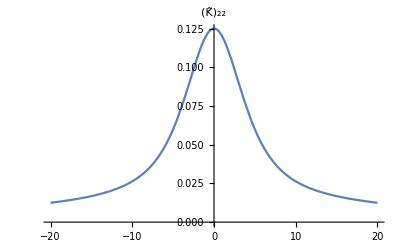
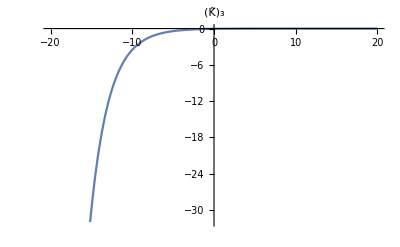
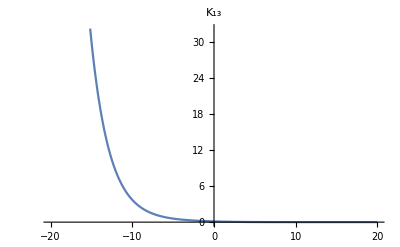
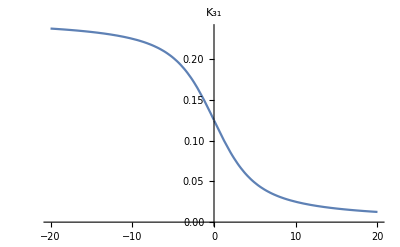

```mathematica
Table[Plot[f[s],{s,-20,20},MeshFunctions->Function@@@{{{s,t},s},{{s,t},t}},MeshStyle->{Yellow},PlotLabel->f,Ticks->None],{f,$TrigFunctions}]
```

### a_2

```mathematica
Simplify[funonelogkδ1δ1[s]*Subscript[δ, 1][Subscript[δ, 1][h]] + funonelogkδ1δ3[s]*Subscript[δ, 1][Subscript[δ, 3][h]] + funonelogkδ2δ2[s]*Subscript[δ, 2][Subscript[δ, 2][h]] + funonelogkδ2δ3[s]*Subscript[δ, 2][Subscript[δ, 3][h]] + funonelogkδ3δ3[s]*Subscript[δ, 3][Subscript[δ, 3][h]]+funtwologkδ1δ1[s,t]*Subscript[δ, 1][h]*Subscript[δ, 1][h] + funtwologkδ1δ2[s,t]*Subscript[δ, 1][h]*Subscript[δ, 2][h] + funtwologkδ1δ3[s,t]*Subscript[δ, 1][h]*Subscript[δ, 3][h] + funtwologkδ2δ1[s,t]*Subscript[δ, 2][h]*Subscript[δ, 1][h] +funtwologkδ2δ2[s,t]*Subscript[δ, 2][h]*Subscript[δ, 2][h] +
funtwologkδ2δ3[s,t]*Subscript[δ, 2][h]*Subscript[δ, 3][h] +funtwologkδ3δ1[s,t]*Subscript[δ, 3][h]*Subscript[δ, 1][h] +
funtwologkδ3δ2[s,t]*Subscript[δ, 3][h]*Subscript[δ, 2][h] +
funtwologkδ3δ3[s,t]*Subscript[δ, 3][h]*Subscript[δ, 3][h]]
```

```mathematica
{{1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),0,1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{0,1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 (-1+ⅇ^s)^2 s)ⅇ^(-s/2) ((4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]]+(4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^(-t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) ((-1+ⅇ^t)^2 (-1+3 ⅇ^s+ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(-1+ⅇ^s) t (-2+ⅇ^(2 (s+t)) (2-3 t)+ⅇ^(2 s+3 t) (-2+t)+ⅇ^(2 t) t-ⅇ^(s+t) t+2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^t (2+t))+(-1+ⅇ^(s+t)) s (2+t+2 ⅇ^(2 t) t+4 ⅇ^(s+t) (1+t)-ⅇ^t (2+t)+ⅇ^(2 (s+t)) (2+t)-ⅇ^(s+2 t) (2+t)-ⅇ^s (2+3 t)-ⅇ^(2 s+t) (2+3 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((1+ⅇ^(2 s) (-1+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2)}}
```

{{1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_1[δ_1[h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_2[δ_2[h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) δ_3[δ_3[h]])/k^2),0,1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) δ_1[δ_3[h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_1[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_1[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{0,1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_1[δ_1[h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_2[δ_2[h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) δ_3[δ_3[h]])/k^2),1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) δ_2[δ_3[h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_2[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_2[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{1/(4 k s)(((-1+ⅇ^s-s) δ_1[δ_3[h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_1[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_1[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 k s)(((-1+ⅇ^s-s) δ_2[δ_3[h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_2[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_2[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 (-1+ⅇ^s)^2 s)ⅇ^(-s/2) ((4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) δ_1[δ_1[h]]+(4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) δ_2[δ_2[h]]-(ⅇ^(-t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) ((-1+ⅇ^t)^2 (-1+3 ⅇ^s+ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(-1+ⅇ^s) t (-2+ⅇ^(2 (s+t)) (2-3 t)+ⅇ^(2 s+3 t) (-2+t)+ⅇ^(2 t) t-ⅇ^(s+t) t+2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^t (2+t))+(-1+ⅇ^(s+t)) s (2+t+2 ⅇ^(2 t) t+4 ⅇ^(s+t) (1+t)-ⅇ^t (2+t)+ⅇ^(2 (s+t)) (2+t)-ⅇ^(s+2 t) (2+t)-ⅇ^s (2+3 t)-ⅇ^(2 s+t) (2+3 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((1+ⅇ^(2 s) (-1+s)+s) δ_3[δ_3[h]])/k^2)}}

```mathematica
{{1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),0,1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{0,1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 (-1+ⅇ^s)^2 s)ⅇ^(-s/2) ((4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]]+(4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^(-t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) ((-1+ⅇ^t)^2 (-1+3 ⅇ^s+ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(-1+ⅇ^s) t (-2+ⅇ^(2 (s+t)) (2-3 t)+ⅇ^(2 s+3 t) (-2+t)+ⅇ^(2 t) t-ⅇ^(s+t) t+2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^t (2+t))+(-1+ⅇ^(s+t)) s (2+t+2 ⅇ^(2 t) t+4 ⅇ^(s+t) (1+t)-ⅇ^t (2+t)+ⅇ^(2 (s+t)) (2+t)-ⅇ^(s+2 t) (2+t)-ⅇ^s (2+3 t)-ⅇ^(2 s+t) (2+3 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((1+ⅇ^(2 s) (-1+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2)}} -((ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))-(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)+(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))-(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)+(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) (Subscript[δ, 3][h])^2)/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 s t (s+t))+(ⅇ^(-s/2) (1-ⅇ^(2 s)+2 ⅇ^s s) Subscript[δ, 3][Subscript[δ, 3][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 k^2 s))*IdentityMatrix[3]
```

```mathematica
Simplify[{{-((ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t)))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) (Subscript[δ, 3][h])^2)/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 s t (s+t))-(ⅇ^(-s/2) (1-ⅇ^(2 s)+2 ⅇ^s s) Subscript[δ, 3][Subscript[δ, 3][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 k^2 s)+1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),0,1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{0,-((ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t)))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) (Subscript[δ, 3][h])^2)/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 s t (s+t))-(ⅇ^(-s/2) (1-ⅇ^(2 s)+2 ⅇ^s s) Subscript[δ, 3][Subscript[δ, 3][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 k^2 s)+1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 1][Subscript[δ, 1][h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2),1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 1][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 1][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 k s)(((-1+ⅇ^s-s) Subscript[δ, 2][Subscript[δ, 3][h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) Subscript[δ, 2][h] Subscript[δ, 3][h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),-((ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t)))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) (Subscript[δ, 3][h])^2)/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 s t (s+t))-(ⅇ^(-s/2) (1-ⅇ^(2 s)+2 ⅇ^s s) Subscript[δ, 3][Subscript[δ, 3][h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 k^2 s)+1/(4 (-1+ⅇ^s)^2 s)ⅇ^(-s/2) ((4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 1][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 1][Subscript[δ, 1][h]]+(4 ⅇ^(s+t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) (Subscript[δ, 2][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))-ⅇ^s (2+ⅇ^s (-2+s)+s) Subscript[δ, 2][Subscript[δ, 2][h]]-(ⅇ^(-t/2) (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) ((-1+ⅇ^t)^2 (-1+3 ⅇ^s+ⅇ^(s+t)+ⅇ^(2 s+t)) s^2+(-1+ⅇ^s) t (-2+ⅇ^(2 (s+t)) (2-3 t)+ⅇ^(2 s+3 t) (-2+t)+ⅇ^(2 t) t-ⅇ^(s+t) t+2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^t (2+t))+(-1+ⅇ^(s+t)) s (2+t+2 ⅇ^(2 t) t+4 ⅇ^(s+t) (1+t)-ⅇ^t (2+t)+ⅇ^(2 (s+t)) (2+t)-ⅇ^(s+2 t) (2+t)-ⅇ^s (2+3 t)-ⅇ^(2 s+t) (2+3 t))) (Subscript[δ, 3][h])^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((1+ⅇ^(2 s) (-1+s)+s) Subscript[δ, 3][Subscript[δ, 3][h]])/k^2)}}]
```

{{1/(4 s)((4 ⅇ^((s+t)/2) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_1[δ_1[h]])/((-1+ⅇ^s)^2)+(4 ⅇ^((s+t)/2) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_2[δ_2[h]])/((-1+ⅇ^s)^2)+(ⅇ^(1/2 (-s-t)) ((-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2-(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))-(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) δ_3[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+(ⅇ^(-s/2) (-1+ⅇ^(2 s)-2 ⅇ^s s) δ_3[δ_3[h]])/((-1+ⅇ^s)^2 k^2)+1/((-1+ⅇ^s)^2)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_1[δ_1[h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_2[δ_2[h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) δ_3[δ_3[h]])/k^2)),0,1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) δ_1[δ_3[h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_1[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_1[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{0,1/(4 s)((4 ⅇ^((s+t)/2) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_1[δ_1[h]])/((-1+ⅇ^s)^2)+(4 ⅇ^((s+t)/2) (-ⅇ^s (-1+ⅇ^t)^2 s^2-(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))+(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_2[δ_2[h]])/((-1+ⅇ^s)^2)+(ⅇ^(1/2 (-s-t)) ((-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2-(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))-(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) δ_3[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+(ⅇ^(-s/2) (-1+ⅇ^(2 s)-2 ⅇ^s s) δ_3[δ_3[h]])/((-1+ⅇ^s)^2 k^2)+1/((-1+ⅇ^s)^2)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_1[δ_1[h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_2[δ_2[h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) δ_3[δ_3[h]])/k^2)),1/(4 k s)ⅇ^(-s/2) (((1+ⅇ^s (-1+s)) δ_2[δ_3[h]])/(-1+ⅇ^s)+(2 ⅇ^(-t/2) (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_2[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))-(2 ⅇ^(-t/2) (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_2[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t)))},{1/(4 k s)(((-1+ⅇ^s-s) δ_1[δ_3[h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_1[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_1[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),1/(4 k s)(((-1+ⅇ^s-s) δ_2[δ_3[h]])/(-1+ⅇ^s)-(2 (t+ⅇ^(2 s+t) t+ⅇ^s (s^2-t+s t)-ⅇ^(s+t) (s^2+t+s t)) δ_2[h] δ_3[h])/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))+(2 (-ⅇ^t (-1+ⅇ^s) t^2+s (1+ⅇ^(s+2 t)+ⅇ^t (-1+t)-ⅇ^(s+t) (1+t))) δ_2[h] δ_3[h])/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^((s+t)/2)) (1+ⅇ^((s+t)/2)) t (s+t))),(ⅇ^(1/2 (-s-t)) (2 ((-1+ⅇ^t) s-ⅇ^t (-1+ⅇ^s) t) δ_3[h]^2+ⅇ^(t/2) (-1+ⅇ^(s+t)) s t δ_3[δ_3[h]]))/(4 (-1+ⅇ^(s+t)) k^2 s t)}}

```mathematica
Out[109][[1,1]]
```

-((ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t)))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_1[δ_1[h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^((s+t)/2) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 s t (s+t))+(ⅇ^(s/2) (2+ⅇ^s (-2+s)+s) δ_2[δ_2[h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 s)-(ⅇ^(1/2 (-s-t)) (-(-1+ⅇ^t)^2 (1+ⅇ^s-ⅇ^(s+t)+3 ⅇ^(2 s+t)) s^2+(-1+ⅇ^(s+t)) s (-2+ⅇ^t (2-5 t)+ⅇ^(s+2 t) (2-5 t)+ⅇ^(2 (s+t)) (-2+t)+4 ⅇ^(s+t) (-1+t)+t+2 ⅇ^(2 t) t+ⅇ^s (2+t)+ⅇ^(2 s+t) (2+t))+(-1+ⅇ^s) t (2+ⅇ^(2 (s+t)) (-2+t)+ⅇ^(2 t) t+3 ⅇ^(s+t) t-2 ⅇ^(s+2 t) t-ⅇ^(s+3 t) t+ⅇ^(2 s+3 t) (2+t)-ⅇ^t (2+3 t))) δ_3[h]^2)/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 s t (s+t))-(ⅇ^(-s/2) (1-ⅇ^(2 s)+2 ⅇ^s s) δ_3[δ_3[h]])/(4 (-1+ⅇ^(s/2))^2 (1+ⅇ^(s/2))^2 k^2 s)+1/(4 (-1+ⅇ^s)^2 s)((2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_1[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_1[δ_1[h]]+(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (1+ⅇ^(s+t)) (ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t))) δ_2[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 t (s+t))+(-1+ⅇ^(2 s)-2 ⅇ^s s) δ_2[δ_2[h]]-(ⅇ^-s (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (ⅇ^(3 (s+t)) s (s+t)-ⅇ^(2 s+3 t) s (s+t)-t (s+t)+ⅇ^t t (s+t)-7 ⅇ^(2 s+t) (s^2-t^2)+ⅇ^(s+2 t) (s^2-t^2)+ⅇ^(3 s+t) (s^2+(4-3 t) t-2 s (2+t))+ⅇ^(2 s) (3 s^2+2 s (2+t)-t (4+t))+ⅇ^s (s^2+2 t (2+t)+s (-4+3 t))-ⅇ^(3 s+2 t) (2 s^2+t (4+t)+s (-4+3 t))+ⅇ^(2 (s+t)) (5 s^2+2 t (2+t)+s (-4+7 t))-ⅇ^(s+t) (2 s^2+t (4+5 t)+s (-4+7 t))) δ_3[h]^2)/((-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (-1+ⅇ^(s+t))^2 k^2 t (s+t))+((2+ⅇ^s (-2+s)+s) δ_3[δ_3[h]])/k^2)

```mathematica
Limit[Limit[Out[110],s-> 0],t->0]
```

(k^2 δ_1[δ_1[h]]+k^2 δ_2[δ_2[h]]-2 δ_3[h]^2+δ_3[δ_3[h]])/(8 k^2)

```mathematica
Limit[Limit[Out[109],s-> 0],t->0]
```

{{(k^2 δ_1[δ_1[h]]+k^2 δ_2[δ_2[h]]-2 δ_3[h]^2+δ_3[δ_3[h]])/(8 k^2),0,δ_1[δ_3[h]]/(8 k)},{0,(k^2 δ_1[δ_1[h]]+k^2 δ_2[δ_2[h]]-2 δ_3[h]^2+δ_3[δ_3[h]])/(8 k^2),δ_2[δ_3[h]]/(8 k)},{δ_1[δ_3[h]]/(8 k),δ_2[δ_3[h]]/(8 k),(-δ_3[h]^2+δ_3[δ_3[h]])/(4 k^2)}}

```mathematica
Simplify[Coefficient[Out[110],(Subscript[δ, 1][h])^2]]
```

(ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t)))/(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (1+ⅇ^((s+t)/2))^2 s t (s+t))

```mathematica
Simplify[Coefficient[Out[110],(Subscript[δ, 2][h])^2]]
```

(ⅇ^s (-1+ⅇ^t)^2 s^2+(-1+ⅇ^(s+t)) s (1+ⅇ^(s+t)+ⅇ^t (-1+t)-ⅇ^s (1+t))-(-1+ⅇ^s) t (1+ⅇ^(s+2 t)+ⅇ^(s+t) (-1+t)-ⅇ^t (1+t)))/(2 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (1+ⅇ^((s+t)/2))^2 s t (s+t))

```mathematica
Simplify[Coefficient[Out[110],(Subscript[δ, 3][h])^2]]
```

(ⅇ^(-s-t/2) (ⅇ^(s+(5 t)/2) s (s+t)-ⅇ^(2 s+(5 t)/2) s (s+t)+ⅇ^(t/2) t (s+t)-ⅇ^(3 t/2) t (s+t)+ⅇ^(s/2) (s^2+s (-2+t)+2 t)+ⅇ^(s+t/2) (s^2-s t-2 t^2)-2 ⅇ^((3 s)/2+t) (s^2-t^2)-2 ⅇ^(s+(3 t)/2) (s^2-t^2)+ⅇ^(s/2+2 t) (s^2-t^2)+ⅇ^(2 s+(3 t)/2) (2 s^2+s t-t^2)+ⅇ^(2 s+t/2) (-s^2+t^2)+ⅇ^(3 s/2) (s^2-2 t+s (2+t))-ⅇ^((5 s)/2+t) ((-2+t) t+s (2+t))-ⅇ^((5 s)/2+2 t) (s (-2+t)+t (2+t))+ⅇ^((3 s)/2+2 t) (s^2+2 t (1+t)+s (-2+3 t))-ⅇ^(s/2+t) (2 s^2+t (2+t)+s (-2+3 t))))/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (1+ⅇ^((s+t)/2))^2 k^2 s t (s+t))

```mathematica
Simplify[Coefficient[Out[110],Subscript[δ, 1][Subscript[δ, 1][h]]]]
```

(-1+ⅇ^s+ⅇ^(s/2) s)/(4 (1+ⅇ^(s/2))^2 s)

```mathematica
Simplify[Coefficient[Out[110],Subscript[δ, 2][Subscript[δ, 2][h]]]]
```

(-1+ⅇ^s+ⅇ^(s/2) s)/(4 (1+ⅇ^(s/2))^2 s)

```mathematica
Simplify[Coefficient[Out[110],Subscript[δ, 3][Subscript[δ, 3][h]]]]
```

(ⅇ^(-s/2) (-1+ⅇ^s+ⅇ^(s/2) s))/(4 (1+ⅇ^(s/2))^2 k^2 s)

```mathematica
Simplify[Subscript[K, 3][s]-Subscript[K, 2][s]]
```

(ⅇ^(-s/2) (-1+ⅇ^s+ⅇ^(s/2) s))/(4 (1+ⅇ^(s/2))^2 s)

```mathematica
Limit[Subscript[K, 3][s]-Subscript[K, 2][s],s-> 0]
```

1/8

```mathematica
Simplify[Coefficient[Out[109][[3,3]],Subscript[δ, 3][Subscript[δ, 3][h]]]]
```

ⅇ^(-s/2)/(4 k^2)

```mathematica
Simplify[Subscript[K, 33][s]-Subscript[K, 2][s]]
```

ⅇ^(-s/2)/4

```mathematica
Out[215]/.{h->h[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],k->E^h[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]}/.{Subscript[δ, j_]->Function[u,-I*D[u,Subscript[x, j]]]}
```

{{1/8 ⅇ^(-2 h[x_1,x_2,x_3]) (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) h^(0,2,0)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) h^(2,0,0)[x_1,x_2,x_3]),0,-1/8 ⅇ^(-h[x_1,x_2,x_3]) h^(1,0,1)[x_1,x_2,x_3]},{0,1/8 ⅇ^(-2 h[x_1,x_2,x_3]) (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) h^(0,2,0)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) h^(2,0,0)[x_1,x_2,x_3]),-1/8 ⅇ^(-h[x_1,x_2,x_3]) h^(0,1,1)[x_1,x_2,x_3]},{-1/8 ⅇ^(-h[x_1,x_2,x_3]) h^(1,0,1)[x_1,x_2,x_3],-1/8 ⅇ^(-h[x_1,x_2,x_3]) h^(0,1,1)[x_1,x_2,x_3],1/4 ⅇ^(-2 h[x_1,x_2,x_3]) ((h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3])}}

```mathematica
Subscript[R, 1k]={{1,0,0},{0,1,0},{0,0,k}}
```

{{1,0,0},{0,1,0},{0,0,k}}

```mathematica
Inverse[Subscript[R, 1k]]
```

{{1,0,0},{0,1,0},{0,0,1/k}}

```mathematica
Simplify[(Subscript[R, 1k].Out[219].Inverse[Subscript[R, 1k]])/.{k-> E^h[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]}]
```

{{1/8 ⅇ^(-2 h[x_1,x_2,x_3]) (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) (h^(0,2,0)[x_1,x_2,x_3]+h^(2,0,0)[x_1,x_2,x_3])),0,-1/8 ⅇ^(-2 h[x_1,x_2,x_3]) h^(1,0,1)[x_1,x_2,x_3]},{0,1/8 ⅇ^(-2 h[x_1,x_2,x_3]) (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) (h^(0,2,0)[x_1,x_2,x_3]+h^(2,0,0)[x_1,x_2,x_3])),-1/8 ⅇ^(-2 h[x_1,x_2,x_3]) h^(0,1,1)[x_1,x_2,x_3]},{-1/8 h^(1,0,1)[x_1,x_2,x_3],-1/8 h^(0,1,1)[x_1,x_2,x_3],1/4 ⅇ^(-2 h[x_1,x_2,x_3]) ((h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3])}}

```mathematica
Simplify[(Subscript[R, 1k].Out[219].Inverse[Subscript[R, 1k]])*E^(2*h[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]])/.{k-> E^h[Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]}]
```

{{1/8 (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) (h^(0,2,0)[x_1,x_2,x_3]+h^(2,0,0)[x_1,x_2,x_3])),0,-1/8 h^(1,0,1)[x_1,x_2,x_3]},{0,1/8 (2 (h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3]-ⅇ^(2 h[x_1,x_2,x_3]) (h^(0,2,0)[x_1,x_2,x_3]+h^(2,0,0)[x_1,x_2,x_3])),-1/8 h^(0,1,1)[x_1,x_2,x_3]},{-1/8 ⅇ^(2 h[x_1,x_2,x_3]) h^(1,0,1)[x_1,x_2,x_3],-1/8 ⅇ^(2 h[x_1,x_2,x_3]) h^(0,1,1)[x_1,x_2,x_3],1/4 ((h^(0,0,1)[x_1,x_2,x_3])^2-h^(0,0,2)[x_1,x_2,x_3])}}

```mathematica
Simplify[Coefficient[Out[109][[3,3]],Subscript[δ, 3][Subscript[δ, 3][h]]]]
```

ⅇ^(-s/2)/(4 k^2)

```mathematica
Simplify[Subscript[H, 3][s,t]-Subscript[H, 2][s,t]]
```

(ⅇ^(-s-t/2) (ⅇ^(s+(5 t)/2) s (s+t)-ⅇ^(2 s+(5 t)/2) s (s+t)+ⅇ^(t/2) t (s+t)-ⅇ^(3 t/2) t (s+t)+ⅇ^(s/2) (s^2+s (-2+t)+2 t)+ⅇ^(s+t/2) (s^2-s t-2 t^2)-2 ⅇ^((3 s)/2+t) (s^2-t^2)-2 ⅇ^(s+(3 t)/2) (s^2-t^2)+ⅇ^(s/2+2 t) (s^2-t^2)+ⅇ^(2 s+(3 t)/2) (2 s^2+s t-t^2)+ⅇ^(2 s+t/2) (-s^2+t^2)+ⅇ^(3 s/2) (s^2-2 t+s (2+t))-ⅇ^((5 s)/2+t) ((-2+t) t+s (2+t))-ⅇ^((5 s)/2+2 t) (s (-2+t)+t (2+t))+ⅇ^((3 s)/2+2 t) (s^2+2 t (1+t)+s (-2+3 t))-ⅇ^(s/2+t) (2 s^2+t (2+t)+s (-2+3 t))))/(4 (-1+ⅇ^(s/2)) (1+ⅇ^(s/2)) (-1+ⅇ^(t/2)) (1+ⅇ^(t/2)) (1+ⅇ^((s+t)/2))^2 s t (s+t))

```mathematica
Simplify[%/%%]
```

k^2